## StringyFNQuarksEnv - Examples

### Loading Package

```mathematica
<<StringyFNQuarksEnv`
SetOptions[StringyFNQuarksEnv,
{"nSinglet"->5,"nNonperts"->0,"nU1s"->5,"nChargeVec"->{1,1,1,1,1},"factorFitnessH"->1,"factorFitnessQ"->2,"factorFitnessCKM"->2,"factorFitnessGS"->30,"factorFitnessNAF"->30,"factorFitnessTEX"->5,"factorFitnessO1"->0.01,"FitRange"->-20,"MethodGenOps"->"Graph","fitTextFac"->{1,0.25,1,1}}];
fixO1coeffvec=Get["Documents/GitHub/string_inspired_MSSM_code/c_version/simlenv/current_ver_2.4.0/opts/o1coeff.txt"];
SetO1Coeff[fixO1coeffvec];
```

StringyFNQuarksEnv: RL/GA Environment for Froggatt-Nielsen Mass Model Building with Non-pertubative Effects

Last updated 16 Aug, 2024 by Lucas Leung.

Execute ?StringyFNQuarksEnv for help. Current StringyFNQuarksEnv options:

{nU1s→4,nChargeVec→{1,1,1,2},nSinglet→2,nNonperts→2,ΦChargeRange→{-7,8},DimOp→5,DimOpofΦ→2,bitsforϕ→3,bitsforΦ→3,BundleModuliFields→Global`ϕ,KahlerEffFields→Global`Φ,VEVsScale→Global`ϵ,ϕVEVmin→0.01,ϕVEVlogGen→1.01,ΦVEVmin→0.001,ΦVEVlogGen→1.01,fixedCharges→True,tenQ→{1,2,5},fiveBarHiggsQ→{4,5},O1CoeffRange→{0.5,3},numOfO1Coeff→10000,O1CoeffVarDiff→0.001,MethodGenOps→List,FitRange→-50,factorFitnessH→10,factorFitnessRG→1,factorFitnessQ→2,factorFitnessCKM→2,factorFitnessGS→20,factorFitnessNAF→20,factorFitnessTEX→10,factorFitnessO1→5,MaxLogPower→10,indPenal→False,diffPenal→False,indFitMax→1,fitDownFac→{1,1,1},fitUpFac→{1,1,1},fitCKMFac→{1,1,1,1,1,1,1,1,1},fitTextFac→{1,1,1,1},v→174,vErr→0.17,mu→{0.00216,1.27,172.69},md→{0.00467,0.0934,4.18},CKMmat→{{0.97373,0.2243,0.00382},{0.221,0.975,0.0408},{0.0086,0.0415,1.014}}}

## Examples for Auxiliary Modules

### StateGenModules

#### RandomStatewithVEVs

```mathematica
RandomStatewithVEVs[]
```

{1,2,5,1,4,4,2,3,3,4,5,3,2,1,5,1,1,3,2,5,2,6,5,7,2,4}

#### ConvertStatewithVEVs

```mathematica
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
ConvertStatewithVEVs[testSV]
```

<|Qq→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},Qd→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qu→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QL→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qe→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QHd→{{0,0,0,1,1}},QHu→{{0,0,0,-1,-1}},Qϕ→{{0,0,1,-1,0},{1,-1,0,0,0},{0,1,-1,0,0},{-1,0,0,0,1},{0,0,0,1,-1}},QΦ→{},ϕVEVs→{0.010303,0.010406,0.0106152,0.010406,0.0101},ΦVEVs→{}|>

#### StateVectoMatwithVEVs

```mathematica
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
StateVectoMatwithVEVs[testSV]
```

{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1},{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0},{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1},{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0},{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1},{0,0,0,1,1},{0,0,0,-1,-1},{0,0,1,-1,0},{1,-1,0,0,0},{0,1,-1,0,0},{-1,0,0,0,1},{0,0,0,1,-1}}

#### StateVectoVEVs

```mathematica
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
StateVectoVEVs[testSV]
```

{ϕ[1]→0.010303,ϕ[2]→0.010406,ϕ[3]→0.0106152,ϕ[4]→0.010406,ϕ[5]→0.0101}

#### AssocFormToStateVec

```mathematica
testAssoc=<|"Q10"->{1,2,5},"Q5b"->{{1,2},{1,2},{1,2}},"Q5bH"->{4,5},"Q1"->{{3,4},{1,2},{2,3},{5,1},{4,5}},"ϕVEVs"->{3,4,6,4,1}|>;
AssocFormToStateVec[testAssoc]
```

{1,2,5,1,1,1,2,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1}

#### AssocFormToVEVs

```mathematica
testAssoc=<|"Q10"->{1,2,5},"Q5b"->{{1,2},{1,2},{1,2}},"Q5bH"->{4,5},"Q1"->{{3,4},{1,2},{2,3},{5,1},{4,5}},"ϕVEVs"->{3,4,6,4,1},"ΦVEVs"->{}|>;
AssocFormToVEVs[testAssoc]
```

{ϕ[1]→3,ϕ[2]→4,ϕ[3]→6,ϕ[4]→4,ϕ[5]→1}

```mathematica
KeyExistsQ[testAssoc,"do"]
```

False

#### ConvertStateVecToVEVPowers

```mathematica
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
ConvertStateVecToVEVPowers[testSV]
```

<|ϕVEVPowers→{3,4,6,4,1},ΦVEVPowers→{}|>

### BitGenModules

#### GADetermDimStateVecwithVEVs

```mathematica
GADetermDimStateVecwithVEVs[]
```

{64,4,15}

#### GARandomStatewithVEVs

```mathematica
GARandomStatewithVEVs[]
```

{0,1,1,0,1,1,1,1,1,0,0,0,1,0,0,0,0,1,0,1,1,1,0,1,0,0,0,0,1,0,1,1,0,0,0,1,1,0,1,1,0,0,1,0,0,0,1,1,1,0,1,1,0,1,1,1,0,0,0,0,0,1,0,1}

#### GAConvertBitlstStateVecwithVEVs

```mathematica
testBits={0,1,1,0,1,1,1,1,1,0,0,0,1,0,0,0,0,1,0,1,1,1,0,1,0,0,0,0,1,0,1,1,0,0,0,1,1,0,1,1,0,0,1,0,0,0,1,1,1,0,1,1,0,1,1,1,0,0,0,0,0,1,0,1};
GAConvertBitlstStateVecwithVEVs[testBits]
```

{3,3,5,2,3,2,4,5,2,5,5,3,3,2,3,2,2,5,1,5,3,3,3,4,0,5}

#### GADetermDimStateVecFix

```mathematica
GADetermDimStateVecFix[]
```

{53,4,15}

#### GARandomStateFix

```mathematica
GARandomStateFix[]
```

{0,1,1,1,1,1,0,1,1,1,1,1,1,0,1,0,1,1,1,0,1,0,1,1,0,0,0,0,0,0,1,1,0,1,0,0,0,1,0,0,1,0,0,1,1,0,1,1,0,1,1,1,0}

#### GAConvertBitlstStateVecFix

```mathematica
SetOptions[StringyFNQuarksEnv,"fixedCharges"->True];
testBits={0,0,0,1,1,1,0,0,0,1,1,1,1,0,1,0,1,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0,1,0,0,0,1,1,0,1,0,0,1,1,1,0,1,0,1,1,0,0,0};
GAConvertBitlstStateVecFix[testBits]
```

{1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1}

#### GAConvertStateVectoBitlst

```mathematica
SetOptions[StringyFNQuarksEnv,"fixedCharges"->True];
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
GAConvertStateVectoBitlst[testSV]
SetOptions[StringyFNQuarksEnv,"fixedCharges"->False];
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
GAConvertStateVectoBitlst[testSV]
```

{0,0,0,1,1,1,0,0,0,1,1,1,1,0,1,0,1,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0,1,0,0,0,1,1,0,1,0,0,1,1,1,0,1,0,1,1,0,0,0}

{0,0,0,0,1,1,1,1,1,1,1,1,0,1,0,1,1,1,0,1,0,0,0,0,0,0,1,1,0,1,1,0,1,0,1,0,0,1,0,1,0,1,0,0,0,0,1,1,1,0,1,0,0,1,1,1,0,1,0,1,1,0,0,0}

### FindOpsModules

#### QMatRepChange

```mathematica
nQVec="nChargevec"/.Options[StringyFNQuarksEnv];
testQVec={1,0,1,0,0};
QMatRepChange[testQVec,nQVec]
```

{-1,0,-1,-1}

#### FromPowertoOps

```mathematica
testPowerOps={3,2,4,5,2};
FromPowertoOps[testPowerOps]
```

ϕ[1]^3 ϕ[2]^2 ϕ[3]^4 ϕ[4]^5 ϕ[5]^2

```mathematica
FindOpsforWIJawithϕVEVsQsector
```

#### FindOpsforWIJaListwithϕVEVsQsector

```mathematica
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
FindOpsforWIJaListwithϕVEVsQsector[testSV]
```

{{ϕ[1] ϕ[4] ϕ[5]},{ϕ[1] ϕ[4] ϕ[5]},{ϕ[1] ϕ[4] ϕ[5]},{ϕ[1] ϕ[2] ϕ[4] ϕ[5]},{ϕ[1] ϕ[2] ϕ[4] ϕ[5]},{ϕ[1] ϕ[2] ϕ[4] ϕ[5]},{ϕ[1] ϕ[5]},{ϕ[1] ϕ[5]},{ϕ[1] ϕ[5]},{ϕ[4]^2 ϕ[5]},{ϕ[2] ϕ[4]^2 ϕ[5]},{ϕ[4] ϕ[5]},{ϕ[2] ϕ[4]^2 ϕ[5]},{ϕ[2]^2 ϕ[4]^2 ϕ[5]},{ϕ[2] ϕ[4] ϕ[5]},{ϕ[4] ϕ[5]},{ϕ[2] ϕ[4] ϕ[5]},{ϕ[5]}}

#### UpdateVectorWithMinimum

```mathematica
testϕVEVs={2,2,2,4,5};
testϕVEVsDupPos={{3,4}};
UpdateVectorWithMinimum[testϕVEVs,testϕVEVsDupPos]
```

{2,2,2,2,5}

#### MinReplaceListRule

```mathematica
testϕVEVs={2,2,2,4,5};
testϕVEVsDupPos={{3,4}};
MinReplaceListRule[testϕVEVs,testϕVEVsDupPos]
```

{1,1,1,0,1}

#### FindOpsFromGraphMethod

```mathematica
testϕQs={3,2,3,4,4,2,1,1,3,3};
testϕVEVs={2,2,2,4,5};
testQSolve={2,0,-1,-1,0};
FindOpsFromGraphMethod[testϕQs,testϕVEVs,testQSolve]
```

{0,0,2,1,0}

#### GenerateOrderedTuples

```mathematica
GenerateOrderedTuples[2,3]
```

{{0,0,0},{1,0,0},{0,1,0},{0,0,1},{2,0,0},{1,1,0},{1,0,1},{0,2,0},{0,1,1},{0,0,2}}

#### SumChargesByPowers

```mathematica
testKCharges={{2,3,4,1,2},{0,3,2,-3,2},{0,3,2,4,2}};
SumChargesByPowers[{0,1,0},testKCharges]
```

{0,3,2,-3,2}

#### ProcessModPowers

```mathematica
testVec={Null,{2,3,3},{3,3,3},Null};
testVec2={{0,0},{0,1},{1,0},{1,1}};
ProcessModPowers[testVec,testVec2]
```

{{2,3,3,0,1},{3,3,3,1,0}}

#### FindOpsFromGraphAddΦ

```mathematica
SetOptions[StringyFNQuarksEnv,
{"nSinglet"->5,"nNonperts"->2}];
testϕQs={3,2,3,4,4,2,1,1,3,3};
testϕVEVs={2,2,2,4,5};
testQSolve={1,0,0,-1,0};
testΦQs={{2,0,-1,-1,0},{1,0,-1,0,0}};
FindOpsFromGraphAddΦ[testϕQs,testϕVEVs,testQSolve,testΦQs]
```

{{0,0,1,1,0,0,0},{0,0,3,2,0,1,0},{0,0,2,1,0,0,1},{0,0,4,2,0,1,1},{0,0,5,3,0,2,0},{0,0,3,1,0,0,2}}

#### FindOpsforWIJaGraphwithϕVEVsQsector

```mathematica
SetOptions[StringyFNQuarksEnv,
{"nSinglet"->5,"nNonperts"->0}];
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
FindOpsforWIJaGraphwithϕVEVsQsector[testSV]
```

{{1,0,0,1,1},{1,0,0,1,1},{1,0,0,1,1},{1,1,0,1,1},{1,1,0,1,1},{1,1,0,1,1},{1,0,0,0,1},{1,0,0,0,1},{1,0,0,0,1},{0,0,0,2,1},{0,1,0,2,1},{0,0,0,1,1},{0,1,0,2,1},{0,2,0,2,1},{0,1,0,1,1},{0,0,0,1,1},{0,1,0,1,1},{0,0,0,0,1}}

{{ϕ[1] ϕ[4] ϕ[5]},{ϕ[1] ϕ[4] ϕ[5]},{ϕ[1] ϕ[4] ϕ[5]},{ϕ[1] ϕ[2] ϕ[4] ϕ[5]},{ϕ[1] ϕ[2] ϕ[4] ϕ[5]},{ϕ[1] ϕ[2] ϕ[4] ϕ[5]},{ϕ[1] ϕ[5]},{ϕ[1] ϕ[5]},{ϕ[1] ϕ[5]},{ϕ[4]^2 ϕ[5]},{ϕ[2] ϕ[4]^2 ϕ[5]},{ϕ[4] ϕ[5]},{ϕ[2] ϕ[4]^2 ϕ[5]},{ϕ[2]^2 ϕ[4]^2 ϕ[5]},{ϕ[2] ϕ[4] ϕ[5]},{ϕ[4] ϕ[5]},{ϕ[2] ϕ[4] ϕ[5]},{ϕ[5]}}

```mathematica
SetOptions[StringyFNQuarksEnv,
{"nSinglet"->5,"nNonperts"->2}];
testSV={1,2,5,5,2,5,3,3,2,4,5,5,2,3,3,4,3,5,5,3,1,4,0,-7,8,-1,7,-2,-3,-1,-4,7,3,0,5,3,1,3};
FindOpsforWIJaGraphwithϕVEVsQsector[testSV]
```

{{ϕ[2]},{},{ϕ[3]},{},{},{},{},{},{},{},{},{ϕ[5]},{},{},{},{ϕ[5]},{},{}}

### TextModules

#### FromWOpsGetLeadingYukawaMatrix

```mathematica
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
testWOps=FindOpsforWIJaListwithϕVEVsQsector[testSV];
testVEVPowers=ConvertStateVecToVEVPowers[testSV];
FromWOpsGetLeadingYukawaMatrix[testWOps,testVEVPowers]
```

<|YukdLead→{{ϵ^8,ϵ^8,ϵ^8},{ϵ^12,ϵ^12,ϵ^12},{ϵ^4,ϵ^4,ϵ^4}},YukuLead→{{ϵ^9,ϵ^13,ϵ^5},{ϵ^13,ϵ^17,ϵ^9},{ϵ^5,ϵ^9,ϵ}}|>

#### LowestOrderOfMonomialListOneVar

```mathematica
testMonList={ϵ^9,ϵ^13,ϵ^5};
LowestOrderOfMonomialListOneVar[testMonList,Global`ϵ]
```

ϵ^5

#### RemoveCoeffFromMonomial

```mathematica
RemoveCoeffFromMonomial[2 ϵ^5]
```

{ϵ^5}

#### MassHierarchyFromLeadingOrders

```mathematica
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
testWOps=FindOpsforWIJaListwithϕVEVsQsector[testSV];
testVEVPowers=ConvertStateVecToVEVPowers[testSV];
testYukLeadPower=FromWOpsGetLeadingYukawaMatrix[testWOps,testVEVPowers];
MassHierarchyFromLeadingOrders[testYukLeadPower]
```

<|YukUpEigens→{1,9,17},YukDownEigens→{4,8,12},mtPow→1,mbPow→4,mu/mcPow→8,mc/mtPow→8,md/msPow→4,ms/mbPow→4,YukUpMatLead→{{ϵ^9,ϵ^13,ϵ^5},{ϵ^13,ϵ^17,ϵ^9},{ϵ^5,ϵ^9,ϵ}},YukDownMatLead→{{ϵ^8,ϵ^8,ϵ^8},{ϵ^12,ϵ^12,ϵ^12},{ϵ^4,ϵ^4,ϵ^4}},PosOTop→3,PosOBot→3|>

#### IdentifyLowestPowerPos

```mathematica
testList={ϵ^9,ϵ^4,ϵ^5};
IdentifyLowestPowerPos[testList]
```

2

#### LocateExtractO1Coeffs

```mathematica
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
testWOps=FindOpsforWIJaListwithϕVEVsQsector[testSV];
testVEVPowers=ConvertStateVecToVEVPowers[testSV];
testYukLeadPower=FromWOpsGetLeadingYukawaMatrix[testWOps,testVEVPowers];
testMH=MassHierarchyFromLeadingOrders[testYukLeadPower];
LocateExtractO1Coeffs[testWOps,testVEVPowers,testMH,O1CLst]
```

<|O1StartPosList→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},O1LeadPosList→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},O1LeadList→{1.57224,2.45663,-1.3332,1.39238,-1.9314,-1.89724,-1.37332,-2.86913,-1.5806,0.654717,-2.1288,0.840511,-0.622308,-1.50496,1.34836,1.25873,2.71661,-1.04339},O1LeadUpMat→{{0.654717,-2.1288,0.840511},{-0.622308,-1.50496,1.34836},{1.25873,2.71661,-1.04339}},O1LeadDownMat→{{1.57224,2.45663,-1.3332},{1.39238,-1.9314,-1.89724},{-1.37332,-2.86913,-1.5806}},OTopVecPos→18,OBotVecPos→9|>

#### CalcScaleAndHiggsO1Coeff

```mathematica
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
testWOps=FindOpsforWIJaListwithϕVEVsQsector[testSV];
testVEVPowers=ConvertStateVecToVEVPowers[testSV];
testYukLeadPower=FromWOpsGetLeadingYukawaMatrix[testWOps,testVEVPowers];
testMH=MassHierarchyFromLeadingOrders[testYukLeadPower];
CalcScaleAndHiggsO1Coeff[testMH]
```

<|YukUpEigens→{1,9,17},YukDownEigens→{4,8,12},mtPow→1,mbPow→4,mu/mcPow→8,mc/mtPow→8,md/msPow→4,ms/mbPow→4,YukUpMatLead→{{ϵ^9,ϵ^13,ϵ^5},{ϵ^13,ϵ^17,ϵ^9},{ϵ^5,ϵ^9,ϵ}},YukDownMatLead→{{ϵ^8,ϵ^8,ϵ^8},{ϵ^12,ϵ^12,ϵ^12},{ϵ^4,ϵ^4,ϵ^4}},PosOTop→3,PosOBot→3,ListOfScales→{0.450642,0.541149,0.472871,0.386627},BestScale→0.459511,HiggsSquared→{375.813,93.7546},BestO1Top→2.56385|>

#### GeometricStandardDeviation

```mathematica
GeometricStandardDeviation[{0.3,0.2,0.1}]
```

1.57397

#### FitnessTexture

```mathematica
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
testWOps=FindOpsforWIJaListwithϕVEVsQsector[testSV];
testVEVPowers=ConvertStateVecToVEVPowers[testSV];
testYukLeadPower=FromWOpsGetLeadingYukawaMatrix[testWOps,testVEVPowers];
testMH=MassHierarchyFromLeadingOrders[testYukLeadPower];
testMH0=CalcScaleAndHiggsO1Coeff[testMH];
FitnessTexture[testMH0,testVEVPowers]
```

<|FitnessTextSec→0.281924,FitnessPowers→0,VarsScale→1.1277,ScalePenalty→0,OTopPenalty→0|>

### OpsToMatModules

#### AdjoinO1coeffWOpsTextQSec

```mathematica
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
testWOps=FindOpsforWIJaListwithϕVEVsQsector[testSV];
testVEVPowers=ConvertStateVecToVEVPowers[testSV];
testYukLeadPower=FromWOpsGetLeadingYukawaMatrix[testWOps,testVEVPowers];
testMH=MassHierarchyFromLeadingOrders[testYukLeadPower];
testMH0=CalcScaleAndHiggsO1Coeff[testMH];
testO1Assoc=LocateExtractO1Coeffs[testWOps,testVEVPowers,testMH,O1coefflist];
AdjoinO1coeffWOpsTextQSec[testWOps,testMH0,testVEVPowers,testO1Assoc,O1coefflist]
```

<|YdMatVal→{{0.00312526,0.00488322,-0.00265011},{0.000123398,-0.000171168,-0.00016814},{-0.0612288,-0.127919,0.0445845}},YuMatVal→{{0.000598021,-0.0000866926,0.0172196},{-0.0000253426,-2.73246×10^-6,0.0012316},{0.0257876,0.00248136,1.17812}},YdMatOps→{{1.57224 ϕ[1] ϕ[4] ϕ[5],2.45663 ϕ[1] ϕ[4] ϕ[5],-1.3332 ϕ[1] ϕ[4] ϕ[5]},{1.39238 ϕ[1] ϕ[2] ϕ[4] ϕ[5],-1.9314 ϕ[1] ϕ[2] ϕ[4] ϕ[5],-1.89724 ϕ[1] ϕ[2] ϕ[4] ϕ[5]},{-1.37332 ϕ[1] ϕ[5],-2.86913 ϕ[1] ϕ[5],1. ϕ[1] ϕ[5]}},YuMatOps→{{0.654717 ϕ[4]^2 ϕ[5],-2.1288 ϕ[2] ϕ[4]^2 ϕ[5],0.840511 ϕ[4] ϕ[5]},{-0.622308 ϕ[2] ϕ[4]^2 ϕ[5],-1.50496 ϕ[2]^2 ϕ[4]^2 ϕ[5],1.34836 ϕ[2] ϕ[4] ϕ[5]},{1.25873 ϕ[4] ϕ[5],2.71661 ϕ[2] ϕ[4] ϕ[5],2.56385 ϕ[5]}},ytMZVal→1.17812,ybMZVal→0.0445845,O1StartPosList→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},O1LeadPosList→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},O1LeadList→{1.57224,2.45663,-1.3332,1.39238,-1.9314,-1.89724,-1.37332,-2.86913,1.,0.654717,-2.1288,0.840511,-0.622308,-1.50496,1.34836,1.25873,2.71661,2.56385},O1LeadUpMat→{{0.654717,-2.1288,0.840511},{-0.622308,-1.50496,1.34836},{1.25873,2.71661,2.56385}},O1LeadDownMat→{{1.57224,2.45663,-1.3332},{1.39238,-1.9314,-1.89724},{-1.37332,-2.86913,1.}},OTopVecPos→18,OBotVecPos→9|>

### RGModules

#### RGGivenYukMZFindYukMGUT

```mathematica
RGGivenYukMZFindYukMGUT[0.9,0.2]
```

{0.791549,0.0945038}

#### RGGivenYukMGUTFindYukMZ

```mathematica
RGGivenYukMGUTFindYukMZ[0.9,0.2]
```

{0.917094,0.389358}

#### RGGivenYukMZFindYukRatiosAll

```mathematica
RGGivenYukMZFindYukRatiosAll[0.99,0.025]
```

<|ytMZ→0.99,ybMZ→0.025,yu33R→1.75036,yu3iR→1.75648,yuijR→0.843845,yd33R→0.519026,yd3iR→0.408432,ydijR→0.406912|>

#### RGGivenYukMZFindYukRatiosAllFixedPlane

```mathematica
RGGivenYukMZFindYukRatiosAllFixedPlane[0.99,0.025]
```

<|ytMZ→0.99,ybMZ→0.025,yu33R→1.13222,yu3iR→1.09585,yuijR→0.746741,yd33R→0.495998,yd3iR→0.402105,ydijR→0.404733|>

#### ConstructRGFactors

```mathematica
ConstructRGFactors[0.01,0.1,1,3]
```

{1,1,0.1,1,1,0.1,0.1,0.1,0.01}

#### GivenYukMatsFindRGMatricesPlane

```mathematica
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
testWOps=FindOpsforWIJaListwithϕVEVsQsector[testSV];
testVEVPowers=ConvertStateVecToVEVPowers[testSV];
testYukLeadPower=FromWOpsGetLeadingYukawaMatrix[testWOps,testVEVPowers];
testMH=MassHierarchyFromLeadingOrders[testYukLeadPower];
testMH0=CalcScaleAndHiggsO1Coeff[testMH];
testO1Assoc=LocateExtractO1Coeffs[testWOps,testVEVPowers,testMH,O1coefflist];
testYukMZVals=AdjoinO1coeffWOpsTextQSec[testWOps,testMH0,testVEVPowers,testO1Assoc,O1coefflist];
GivenYukMatsFindRGMatricesPlane[testYukMZVals]
```

<|RGUpMat→{{4.2037,4.2037,19.9831},{4.2037,4.2037,19.9831},{19.9831,19.9831,19.3386}},RGDownMat→{{0.407029,0.407029,0.425822},{0.407029,0.407029,0.425822},{0.425822,0.425822,1.14176}}|>

#### O1LogDevPenal

```mathematica
O1LogDevPenal[0.4]
```

0.09691

#### FitnessRG

```mathematica
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
testWOps=FindOpsforWIJaListwithϕVEVsQsector[testSV];
testVEVPowers=ConvertStateVecToVEVPowers[testSV];
testYukLeadPower=FromWOpsGetLeadingYukawaMatrix[testWOps,testVEVPowers];
testMH=MassHierarchyFromLeadingOrders[testYukLeadPower];
testMH0=CalcScaleAndHiggsO1Coeff[testMH];
testO1Assoc=LocateExtractO1Coeffs[testWOps,testVEVPowers,testMH,O1coefflist];
testYukMZVals=AdjoinO1coeffWOpsTextQSec[testWOps,testMH0,testVEVPowers,testO1Assoc,O1coefflist];
FitnessRG[testYukMZVals]
```

<|FitnessRGSec→6.4096|>

### SMModules

#### ComputeSMQuantities

```mathematica
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
testWOps=FindOpsforWIJaListwithϕVEVsQsector[testSV];
testVEVPowers=ConvertStateVecToVEVPowers[testSV];
testYukLeadPower=FromWOpsGetLeadingYukawaMatrix[testWOps,testVEVPowers];
testMH=MassHierarchyFromLeadingOrders[testYukLeadPower];
testMH0=CalcScaleAndHiggsO1Coeff[testMH];
testO1Assoc=LocateExtractO1Coeffs[testWOps,testVEVPowers,testMH,O1coefflist];
testYukMZVals=AdjoinO1coeffWOpsTextQSec[testWOps,testMH0,testVEVPowers,testO1Assoc,O1coefflist];
ComputeSMQuantities[testYukMZVals[["YdMatVal"]],testYukMZVals[["YuMatVal"]]]
```

<|Hd→28.0927,Hu→146.53,Higgs→149.199,tanβ→5.21595,CKMmat→{{0.915506,0.402171,-0.0104016},{-0.402096,0.913891,-0.0558803},{0.0129675,-0.0553412,-0.998383}},md→{0.000332632,0.0309974,4.18},mu→{0.00434295,0.0376033,172.69}|>

### FitModules

#### NormalLog

```mathematica
NormalLog[0.3,0.9]
```

0.477121

#### FitnessHiggs

```mathematica
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
testWOps=FindOpsforWIJaListwithϕVEVsQsector[testSV];
testVEVPowers=ConvertStateVecToVEVPowers[testSV];
testYukLeadPower=FromWOpsGetLeadingYukawaMatrix[testWOps,testVEVPowers];
testMH=MassHierarchyFromLeadingOrders[testYukLeadPower];
testMH0=CalcScaleAndHiggsO1Coeff[testMH];
testO1Assoc=LocateExtractO1Coeffs[testWOps,testVEVPowers,testMH,O1coefflist];
testYukMZVals=AdjoinO1coeffWOpsTextQSec[testWOps,testMH0,testVEVPowers,testO1Assoc,O1coefflist];
testMass=ComputeSMQuantities[testYukMZVals[["YdMatVal"]],testYukMZVals[["YuMatVal"]]]
```

```mathematica
FitnessHiggs[testMass]
```

<|FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0|>

#### FitnessQuarksMassMix

```mathematica
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
testWOps=FindOpsforWIJaListwithϕVEVsQsector[testSV];
testVEVPowers=ConvertStateVecToVEVPowers[testSV];
testYukLeadPower=FromWOpsGetLeadingYukawaMatrix[testWOps,testVEVPowers];
testMH=MassHierarchyFromLeadingOrders[testYukLeadPower];
testMH0=CalcScaleAndHiggsO1Coeff[testMH];
testO1Assoc=LocateExtractO1Coeffs[testWOps,testVEVPowers,testMH,O1coefflist];
testYukMZVals=AdjoinO1coeffWOpsTextQSec[testWOps,testMH0,testVEVPowers,testO1Assoc,O1coefflist];
testMass=ComputeSMQuantities[testYukMZVals[["YdMatVal"]],testYukMZVals[["YuMatVal"]]];
FitnessQuarksMassMix[testMass]
```

<|FitnessQMassSec→3.45828,FitnessQMixSec→1.45014,FitnessQmass→{1.14735,0.479021,0.,0.303331,1.52858,0.},FitnessCKM→{0.0267776,0.253581,0.435038,0.259938,0.0281104,0.136599,0.178358,0.125,0.00674065}|>

#### FitnessGSAnomaly

```mathematica
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};testQMat=StateVectoMatwithVEVs[testSV];
FitnessGSAnomaly[testQMat]
```

<|FitnessGSSec→0|>

#### CheckCharge

```mathematica
CheckCharge[{2,3}]
```

0

```mathematica
CheckCharge[{2,2}]
```

2

#### FitnessNonAbelianFactors

```mathematica
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
FitnessNonAbelianFactors[testSV]
```

<|FitnessNAFSec→0|>

#### FitnessCalcQsectorOnly

```mathematica
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
testWOps=FindOpsforWIJaListwithϕVEVsQsector[testSV];
testVEVPowers=ConvertStateVecToVEVPowers[testSV];
testYukLeadPower=FromWOpsGetLeadingYukawaMatrix[testWOps,testVEVPowers];
testMH=MassHierarchyFromLeadingOrders[testYukLeadPower];
testMH0=CalcScaleAndHiggsO1Coeff[testMH];
testO1Assoc=LocateExtractO1Coeffs[testWOps,testVEVPowers,testMH,O1coefflist];
testYukMZVals=AdjoinO1coeffWOpsTextQSec[testWOps,testMH0,testVEVPowers,testO1Assoc,O1coefflist];
testMass=ComputeSMQuantities[testYukMZVals[["YdMatVal"]],testYukMZVals[["YuMatVal"]]];
FitnessCalcQsectorOnly[testMass,testSV,testYukMZVals]
```

<|Fitness→-16.2265,FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0,FitnessRGSec→6.4096,FitnessQMassSec→3.45828,FitnessQMixSec→1.45014,FitnessQmass→{1.14735,0.479021,0.,0.303331,1.52858,0.},FitnessCKM→{0.0267776,0.253581,0.435038,0.259938,0.0281104,0.136599,0.178358,0.125,0.00674065},FitnessGSSec→0,FitnessNAFSec→0|>

### O1Modules

#### ChangeO1VecByAmount

```mathematica
ChangeO1VecByAmount[{0.2,0.3,0.4,0.5},3]
```

{0.2,0.3,0.401,0.5}

#### FitnessO1Coeff

```mathematica
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
testWOps=FindOpsforWIJaListwithϕVEVsQsector[testSV];
testVEVPowers=ConvertStateVecToVEVPowers[testSV];
testYukLeadPower=FromWOpsGetLeadingYukawaMatrix[testWOps,testVEVPowers];
testMH=MassHierarchyFromLeadingOrders[testYukLeadPower];
testMH0=CalcScaleAndHiggsO1Coeff[testMH];
testO1Assoc=LocateExtractO1Coeffs[testWOps,testVEVPowers,testMH,O1CLst];
testYukMZVals=AdjoinO1coeffWOpsTextQSec[testWOps,testMH0,testVEVPowers,testO1Assoc,O1CLst];
testMass=ComputeSMQuantities[testYukMZVals[["YdMatVal"]],testYukMZVals[["YuMatVal"]]];
testMass2=testMass;
AssociateTo[testMass2,"Higgs"->149.2];
FitnessO1Coeff[testMass2,testMass,0.2]
```

<|FitnessO1Sec→2.81645×10^-6,ListofdOdp→{0.00167823,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}|>

### MiscModules

#### DetectBitlist

```mathematica
testBit=GARandomStateFix[];
testBit2={2,0,0};
testBit3={1,0,0,1,0};
DetectBitlist[testBit]
DetectBitlist[testBit2]
DetectBitlist[testBit3]
```

True

False

False

### DataAnalModules

## Examples for Main Module

```mathematica
?StringyFNQuarksEnv
```

### MainModules

#### CompleteStateGivenWOps

```mathematica
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
testWOps=FindOpsforWIJaListwithϕVEVsQsector[testSV];
testVEVPowers=ConvertStateVecToVEVPowers[testSV];
testYukLeadPower=FromWOpsGetLeadingYukawaMatrix[testWOps,testVEVPowers];
testMH=MassHierarchyFromLeadingOrders[testYukLeadPower];
testMH0=CalcScaleAndHiggsO1Coeff[testMH];
testO1Assoc=LocateExtractO1Coeffs[testWOps,testVEVPowers,testMH,O1CLst];
testYukMZVals=AdjoinO1coeffWOpsTextQSec[testWOps,testMH0,testVEVPowers,testO1Assoc,O1CLst];
CompleteStateGivenWOps[testSV,testWOps,testMH0,testVEVPowers,O1CLst]
```

<|Fitness→-16.2265,FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0,FitnessRGSec→6.4096,FitnessQMassSec→3.45828,FitnessQMixSec→1.45014,FitnessQmass→{1.14735,0.479021,0.,0.303331,1.52858,0.},FitnessCKM→{0.0267776,0.253581,0.435038,0.259938,0.0281104,0.136599,0.178358,0.125,0.00674065},FitnessGSSec→0,FitnessNAFSec→0,Hd→28.0927,Hu→146.53,Higgs→149.199,tanβ→5.21595,CKMmat→{{0.915506,0.402171,-0.0104016},{-0.402096,0.913891,-0.0558803},{0.0129675,-0.0553412,-0.998383}},md→{0.000332632,0.0309974,4.18},mu→{0.00434295,0.0376033,172.69},ValueLst→{0,3.45828,1.45014},ϕVEVs→{0.0970259,0.0445845,0.00941402,0.0445845,0.459511},ΦVEVs→{},YukdMatSt→(1.57224 ϕ[1] ϕ[4] ϕ[5] | 2.45663 ϕ[1] ϕ[4] ϕ[5] | -1.3332 ϕ[1] ϕ[4] ϕ[5]
1.39238 ϕ[1] ϕ[2] ϕ[4] ϕ[5] | -1.9314 ϕ[1] ϕ[2] ϕ[4] ϕ[5] | -1.89724 ϕ[1] ϕ[2] ϕ[4] ϕ[5]
-1.37332 ϕ[1] ϕ[5] | -2.86913 ϕ[1] ϕ[5] | 1. ϕ[1] ϕ[5]),YukuMatSt→(0.654717 ϕ[4]^2 ϕ[5] | -2.1288 ϕ[2] ϕ[4]^2 ϕ[5] | 0.840511 ϕ[4] ϕ[5]
-0.622308 ϕ[2] ϕ[4]^2 ϕ[5] | -1.50496 ϕ[2]^2 ϕ[4]^2 ϕ[5] | 1.34836 ϕ[2] ϕ[4] ϕ[5]
1.25873 ϕ[4] ϕ[5] | 2.71661 ϕ[2] ϕ[4] ϕ[5] | 2.56385 ϕ[5])|>

#### CompleteStateO1Coeffs

```mathematica
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
CompleteStateO1Coeffs[testSV,O1CLst]
```

<|Fitness→-19.4372,FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0,FitnessRGSec→5.89936,FitnessQMassSec→3.45828,FitnessQMixSec→1.45014,FitnessQmass→{1.14735,0.479021,0.,0.303331,1.52858,0.},FitnessCKM→{0.0267776,0.253581,0.435038,0.259938,0.0281104,0.136599,0.178358,0.125,0.00674065},FitnessGSSec→0,FitnessNAFSec→0,Hd→28.0927,Hu→146.53,Higgs→149.199,tanβ→5.21595,CKMmat→{{0.915506,0.402171,-0.0104016},{-0.402096,0.913891,-0.0558803},{0.0129675,-0.0553412,-0.998383}},md→{0.000332632,0.0309974,4.18},mu→{0.00434295,0.0376033,172.69},FitnessO1List→{53.0418,23.1004,40.2704,8.24955,2.92587,9.82006,45.2495,27.1976,6.15279,1.27423,4.69519,1.37674,0.133793,1.67461,5.31545,0.658496},FitnessO1Sec→231.136,ValueLst→{0,3.45828,1.45014},ϕVEVs→{0.010303,0.010406,0.0106152,0.010406,0.0101},ΦVEVs→{},YukdMatSt→(1.57224 ϕ[1] ϕ[4] ϕ[5] | 2.45663 ϕ[1] ϕ[4] ϕ[5] | -1.3332 ϕ[1] ϕ[4] ϕ[5]
1.39238 ϕ[1] ϕ[2] ϕ[4] ϕ[5] | -1.9314 ϕ[1] ϕ[2] ϕ[4] ϕ[5] | -1.89724 ϕ[1] ϕ[2] ϕ[4] ϕ[5]
-1.37332 ϕ[1] ϕ[5] | -2.86913 ϕ[1] ϕ[5] | 1. ϕ[1] ϕ[5]),YukuMatSt→(0.654717 ϕ[4]^2 ϕ[5] | -2.1288 ϕ[2] ϕ[4]^2 ϕ[5] | 0.840511 ϕ[4] ϕ[5]
-0.622308 ϕ[2] ϕ[4]^2 ϕ[5] | -1.50496 ϕ[2]^2 ϕ[4]^2 ϕ[5] | 1.34836 ϕ[2] ϕ[4] ϕ[5]
1.25873 ϕ[4] ϕ[5] | 2.71661 ϕ[2] ϕ[4] ϕ[5] | 2.56385 ϕ[5]),StateVec→{1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1},Terminal→True,FitnessTextSec→0.281924,FitnessPowers→0,VarsScale→1.1277,ScalePenalty→0,OTopPenalty→0,Qq→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},Qd→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qu→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QL→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qe→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QHd→{{0,0,0,1,1}},QHu→{{0,0,0,-1,-1}},Qϕ→{{0,0,1,-1,0},{1,-1,0,0,0},{0,1,-1,0,0},{-1,0,0,0,1},{0,0,0,1,-1}},QΦ→{},YukUpEigens→{1,9,17},YukDownEigens→{4,8,12},mtPow→1,mbPow→4,mu/mcPow→8,mc/mtPow→8,md/msPow→4,ms/mbPow→4,YukUpMatLead→{{ϵ^9,ϵ^13,ϵ^5},{ϵ^13,ϵ^17,ϵ^9},{ϵ^5,ϵ^9,ϵ}},YukDownMatLead→{{ϵ^8,ϵ^8,ϵ^8},{ϵ^12,ϵ^12,ϵ^12},{ϵ^4,ϵ^4,ϵ^4}},PosOTop→3,PosOBot→3,ListOfScales→{0.450642,0.541149,0.472871,0.386627},BestScale→0.459511,HiggsSquared→{141235.,8789.93},BestO1Top→2.56385,O1t^2→6.57333|>

#### CompleteStateQsector

```mathematica
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
CompleteStateQsector[testSV]
```

<|Fitness→-18.7339,FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0,FitnessRGSec→6.4096,FitnessQMassSec→3.45828,FitnessQMixSec→1.45014,FitnessQmass→{1.14735,0.479021,0.,0.303331,1.52858,0.},FitnessCKM→{0.0267776,0.253581,0.435038,0.259938,0.0281104,0.136599,0.178358,0.125,0.00674065},FitnessGSSec→0,FitnessNAFSec→0,Hd→28.0927,Hu→146.53,Higgs→149.199,tanβ→5.21595,CKMmat→{{0.915506,0.402171,-0.0104016},{-0.402096,0.913891,-0.0558803},{0.0129675,-0.0553412,-0.998383}},md→{0.000332632,0.0309974,4.18},mu→{0.00434295,0.0376033,172.69},FitnessO1List→{0.0841183,0.0888068,0.20727,0.00310416,0.00291715,0.00614325,0.919927,3.74628,0.258819,0.0016904,0.0447583,0.0400298,0.0000203623,0.00873823,0.076058,0.000251193},FitnessO1Sec→5.48893,ValueLst→{0,3.45828,1.45014},ϕVEVs→{0.010303,0.010406,0.0106152,0.010406,0.0101},ΦVEVs→{},YukdMatSt→(1.57224 ϕ[1] ϕ[4] ϕ[5] | 2.45663 ϕ[1] ϕ[4] ϕ[5] | -1.3332 ϕ[1] ϕ[4] ϕ[5]
1.39238 ϕ[1] ϕ[2] ϕ[4] ϕ[5] | -1.9314 ϕ[1] ϕ[2] ϕ[4] ϕ[5] | -1.89724 ϕ[1] ϕ[2] ϕ[4] ϕ[5]
-1.37332 ϕ[1] ϕ[5] | -2.86913 ϕ[1] ϕ[5] | 1. ϕ[1] ϕ[5]),YukuMatSt→(0.654717 ϕ[4]^2 ϕ[5] | -2.1288 ϕ[2] ϕ[4]^2 ϕ[5] | 0.840511 ϕ[4] ϕ[5]
-0.622308 ϕ[2] ϕ[4]^2 ϕ[5] | -1.50496 ϕ[2]^2 ϕ[4]^2 ϕ[5] | 1.34836 ϕ[2] ϕ[4] ϕ[5]
1.25873 ϕ[4] ϕ[5] | 2.71661 ϕ[2] ϕ[4] ϕ[5] | 2.56385 ϕ[5]),StateVec→{1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1},Terminal→True,FitnessTextSec→0.281924,FitnessPowers→0,VarsScale→1.1277,ScalePenalty→0,OTopPenalty→0,Qq→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},Qd→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qu→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QL→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qe→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QHd→{{0,0,0,1,1}},QHu→{{0,0,0,-1,-1}},Qϕ→{{0,0,1,-1,0},{1,-1,0,0,0},{0,1,-1,0,0},{-1,0,0,0,1},{0,0,0,1,-1}},QΦ→{},YukUpEigens→{1,9,17},YukDownEigens→{4,8,12},mtPow→1,mbPow→4,mu/mcPow→8,mc/mtPow→8,md/msPow→4,ms/mbPow→4,YukUpMatLead→{{ϵ^9,ϵ^13,ϵ^5},{ϵ^13,ϵ^17,ϵ^9},{ϵ^5,ϵ^9,ϵ}},YukDownMatLead→{{ϵ^8,ϵ^8,ϵ^8},{ϵ^12,ϵ^12,ϵ^12},{ϵ^4,ϵ^4,ϵ^4}},PosOTop→3,PosOBot→3,ListOfScales→{0.450642,0.541149,0.472871,0.386627},BestScale→0.459511,HiggsSquared→{141235.,8789.93},BestO1Top→2.56385|>

#### GAFitnessFuncQsector

```mathematica
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
testBits=GAConvertStateVectoBitlst[testSV];
GAFitnessFuncQsector[testBits]
```

<|Fitness→-18.7339,FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0,FitnessRGSec→6.4096,FitnessQMassSec→3.45828,FitnessQMixSec→1.45014,FitnessQmass→{1.14735,0.479021,0.,0.303331,1.52858,0.},FitnessCKM→{0.0267776,0.253581,0.435038,0.259938,0.0281104,0.136599,0.178358,0.125,0.00674065},FitnessGSSec→0,FitnessNAFSec→0,Hd→28.0927,Hu→146.53,Higgs→149.199,tanβ→5.21595,CKMmat→{{0.915506,0.402171,-0.0104016},{-0.402096,0.913891,-0.0558803},{0.0129675,-0.0553412,-0.998383}},md→{0.000332632,0.0309974,4.18},mu→{0.00434295,0.0376033,172.69},FitnessO1List→{0.0841183,0.0888068,0.20727,0.00310416,0.00291715,0.00614325,0.919927,3.74628,0.258819,0.0016904,0.0447583,0.0400298,0.0000203623,0.00873823,0.076058,0.000251193},FitnessO1Sec→5.48893,ValueLst→{0,3.45828,1.45014},ϕVEVs→{0.010303,0.010406,0.0106152,0.010406,0.0101},ΦVEVs→{},YukdMatSt→(1.57224 ϕ[1] ϕ[4] ϕ[5] | 2.45663 ϕ[1] ϕ[4] ϕ[5] | -1.3332 ϕ[1] ϕ[4] ϕ[5]
1.39238 ϕ[1] ϕ[2] ϕ[4] ϕ[5] | -1.9314 ϕ[1] ϕ[2] ϕ[4] ϕ[5] | -1.89724 ϕ[1] ϕ[2] ϕ[4] ϕ[5]
-1.37332 ϕ[1] ϕ[5] | -2.86913 ϕ[1] ϕ[5] | 1. ϕ[1] ϕ[5]),YukuMatSt→(0.654717 ϕ[4]^2 ϕ[5] | -2.1288 ϕ[2] ϕ[4]^2 ϕ[5] | 0.840511 ϕ[4] ϕ[5]
-0.622308 ϕ[2] ϕ[4]^2 ϕ[5] | -1.50496 ϕ[2]^2 ϕ[4]^2 ϕ[5] | 1.34836 ϕ[2] ϕ[4] ϕ[5]
1.25873 ϕ[4] ϕ[5] | 2.71661 ϕ[2] ϕ[4] ϕ[5] | 2.56385 ϕ[5]),Bits→{0,0,0,1,1,1,0,0,0,1,1,1,1,0,1,0,1,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0,1,0,0,0,1,1,0,1,0,0,1,1,1,0,1,0,1,1,0,0,0},StateVec→{1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1},Terminal→True,FitnessTextSec→0.281924,FitnessPowers→0,VarsScale→1.1277,ScalePenalty→0,OTopPenalty→0,Qq→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},Qd→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qu→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QL→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qe→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QHd→{{0,0,0,1,1}},QHu→{{0,0,0,-1,-1}},Qϕ→{{0,0,1,-1,0},{1,-1,0,0,0},{0,1,-1,0,0},{-1,0,0,0,1},{0,0,0,1,-1}},QΦ→{},YukUpEigens→{1,9,17},YukDownEigens→{4,8,12},mtPow→1,mbPow→4,mu/mcPow→8,mc/mtPow→8,md/msPow→4,ms/mbPow→4,YukUpMatLead→{{ϵ^9,ϵ^13,ϵ^5},{ϵ^13,ϵ^17,ϵ^9},{ϵ^5,ϵ^9,ϵ}},YukDownMatLead→{{ϵ^8,ϵ^8,ϵ^8},{ϵ^12,ϵ^12,ϵ^12},{ϵ^4,ϵ^4,ϵ^4}},PosOTop→3,PosOBot→3,ListOfScales→{0.450642,0.541149,0.472871,0.386627},BestScale→0.459511,HiggsSquared→{141235.,8789.93},BestO1Top→2.56385|>

#### GAInitialiseStateQsector

```mathematica
GAInitialiseStateQsector[]
```

<|Fitness→-427.662,FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0,FitnessRGSec→21.4133,FitnessQMassSec→60,FitnessQMixSec→60.0286,FitnessQmass→{10,10,10,10,10,10},FitnessCKM→{0.0115614,10,10,10,0.0109954,10,10,10,0.00603795},FitnessGSSec→0,FitnessNAFSec→1,Hd→vdmax,Hu→vumax,Higgs→√(vdmax^2+vumax^2),tanβ→vumax/vdmax,CKMmat→{{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}},md→{0.,0.,0.},mu→{0.,0.,0.},FitnessO1List→{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},FitnessO1Sec→0.,ValueLst→{0,60,60.0286},ϕVEVs→{0.0101,0.010406,0.010201,0.0105101,0.0107214},ΦVEVs→{},YukdMatSt→(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0),YukuMatSt→(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0),Bits→{0,1,1,1,1,0,1,0,1,0,0,0,0,0,1,1,1,0,0,1,1,0,0,1,0,0,0,0,0,1,0,1,1,0,0,1,1,1,0,0,0,0,1,1,0,0,1,1,0,0,1,1,0},StateVec→{1,2,5,5,2,3,4,5,1,4,5,3,5,1,2,4,2,3,4,3,4,1,4,2,5,7},Terminal→False,FitnessTextSec→27.2382,FitnessPowers→0,VarsScale→1.,ScalePenalty→8.20111,OTopPenalty→18.7871,Qq→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},Qd→{{0,0,0,1,1},{0,1,0,0,1},{1,0,1,0,0}},Qu→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QL→{{0,0,0,1,1},{0,1,0,0,1},{1,0,1,0,0}},Qe→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QHd→{{0,0,0,1,1}},QHu→{{0,0,0,-1,-1}},Qϕ→{{0,-1,1,0,0},{0,0,-1,0,1},{1,0,0,-1,0},{0,1,-1,0,0},{0,0,0,0,0}},QΦ→{},YukUpEigens→{40,40,40},YukDownEigens→{40,40,40},mtPow→40,mbPow→40,mu/mcPow→0,mc/mtPow→0,md/msPow→0,ms/mbPow→0,YukUpMatLead→{{ϵ^40,ϵ^40,ϵ^40},{ϵ^40,ϵ^40,ϵ^40},{ϵ^40,ϵ^40,ϵ^40}},YukDownMatLead→{{ϵ^40,ϵ^40,ϵ^40},{ϵ^40,ϵ^40,ϵ^40},{ϵ^40,ϵ^40,ϵ^40}},PosOTop→1,PosOBot→1,ListOfScales→{3,3,3,3},BestScale→3,HiggsSquared→{2.0176×10^-34,1.18209×10^-37},BestO1Top→8.16334×10^-20|>

## Tests with C code

```mathematica
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
testBits=GAConvertStateVectoBitlst[testSV];
CompleteStateQsector[testSV]
```

<|Fitness→-18.7339,FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0,FitnessRGSec→6.4096,FitnessQMassSec→3.45828,FitnessQMixSec→1.45014,FitnessQmass→{1.14735,0.479021,0.,0.303331,1.52858,0.},FitnessCKM→{0.0267776,0.253581,0.435038,0.259938,0.0281104,0.136599,0.178358,0.125,0.00674065},FitnessGSSec→0,FitnessNAFSec→0,Hd→28.0927,Hu→146.53,Higgs→149.199,tanβ→5.21595,CKMmat→{{0.915506,0.402171,-0.0104016},{-0.402096,0.913891,-0.0558803},{0.0129675,-0.0553412,-0.998383}},md→{0.000332632,0.0309974,4.18},mu→{0.00434295,0.0376033,172.69},FitnessO1List→{0.0841183,0.0888068,0.20727,0.00310416,0.00291715,0.00614325,0.919927,3.74628,0.258819,0.0016904,0.0447583,0.0400298,0.0000203623,0.00873823,0.076058,0.000251193},FitnessO1Sec→5.48893,ValueLst→{0,3.45828,1.45014},ϕVEVs→{0.010303,0.010406,0.0106152,0.010406,0.0101},ΦVEVs→{},YukdMatSt→(1.57224 ϕ[1] ϕ[4] ϕ[5] | 2.45663 ϕ[1] ϕ[4] ϕ[5] | -1.3332 ϕ[1] ϕ[4] ϕ[5]
1.39238 ϕ[1] ϕ[2] ϕ[4] ϕ[5] | -1.9314 ϕ[1] ϕ[2] ϕ[4] ϕ[5] | -1.89724 ϕ[1] ϕ[2] ϕ[4] ϕ[5]
-1.37332 ϕ[1] ϕ[5] | -2.86913 ϕ[1] ϕ[5] | 1. ϕ[1] ϕ[5]),YukuMatSt→(0.654717 ϕ[4]^2 ϕ[5] | -2.1288 ϕ[2] ϕ[4]^2 ϕ[5] | 0.840511 ϕ[4] ϕ[5]
-0.622308 ϕ[2] ϕ[4]^2 ϕ[5] | -1.50496 ϕ[2]^2 ϕ[4]^2 ϕ[5] | 1.34836 ϕ[2] ϕ[4] ϕ[5]
1.25873 ϕ[4] ϕ[5] | 2.71661 ϕ[2] ϕ[4] ϕ[5] | 2.56385 ϕ[5]),StateVec→{1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1},Terminal→True,FitnessTextSec→0.281924,FitnessPowers→0,VarsScale→1.1277,ScalePenalty→0,OTopPenalty→0,Qq→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},Qd→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qu→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QL→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qe→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QHd→{{0,0,0,1,1}},QHu→{{0,0,0,-1,-1}},Qϕ→{{0,0,1,-1,0},{1,-1,0,0,0},{0,1,-1,0,0},{-1,0,0,0,1},{0,0,0,1,-1}},QΦ→{},YukUpEigens→{1,9,17},YukDownEigens→{4,8,12},mtPow→1,mbPow→4,mu/mcPow→8,mc/mtPow→8,md/msPow→4,ms/mbPow→4,YukUpMatLead→{{ϵ^9,ϵ^13,ϵ^5},{ϵ^13,ϵ^17,ϵ^9},{ϵ^5,ϵ^9,ϵ}},YukDownMatLead→{{ϵ^8,ϵ^8,ϵ^8},{ϵ^12,ϵ^12,ϵ^12},{ϵ^4,ϵ^4,ϵ^4}},PosOTop→3,PosOBot→3,ListOfScales→{0.450642,0.541149,0.472871,0.386627},BestScale→0.459511,HiggsSquared→{141235.,8789.93},BestO1Top→2.56385|>

```mathematica
testBits
```

{0,0,0,1,1,1,0,0,0,1,1,1,1,0,1,0,1,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0,1,0,0,0,1,1,0,1,0,0,1,1,1,0,1,0,1,1,0,0,0}

### Pick the right fitness range

#### Fitness for known state

```mathematica
<<StringyFNQuarksEnv`
SetOptions[StringyFNQuarksEnv,
{"nSinglet"->5,"nNonperts"->0,"nU1s"->5,"nChargeVec"->{1,1,1,1,1},"factorFitnessH"->1,"factorFitnessQ"->2,"factorFitnessCKM"->2,"factorFitnessGS"->30,"factorFitnessNAF"->30,"factorFitnessTEX"->5,"factorFitnessO1"->0.02,"factorFitnessRG"->0.1,"FitRange"->-20,"MethodGenOps"->"Graph","fitTextFac"->{1,0.25,1,4},"numOfO1Coeff"->20}];
fixO1coeffvec=Get["Documents/GitHub/string_inspired_MSSM_code/c_version/simlenv/current_ver_2.4.0/opts/o1coeff.txt"];
SetO1Coeff[fixO1coeffvec];
```

StringyFNQuarksEnv: RL/GA Environment for Froggatt-Nielsen Mass Model Building with Non-pertubative Effects

Last updated 16 Aug, 2024 by Lucas Leung.

Execute ?StringyFNQuarksEnv for help. Current StringyFNQuarksEnv options:

{nU1s→4,nChargeVec→{1,1,1,2},nSinglet→2,nNonperts→2,ΦChargeRange→{-7,8},DimOp→5,DimOpofΦ→2,bitsforϕ→3,bitsforΦ→3,BundleModuliFields→Global`ϕ,KahlerEffFields→Global`Φ,VEVsScale→Global`ϵ,ϕVEVmin→0.01,ϕVEVlogGen→1.01,ΦVEVmin→0.001,ΦVEVlogGen→1.01,fixedCharges→True,tenQ→{1,2,5},fiveBarHiggsQ→{4,5},O1CoeffRange→{0.5,3},numOfO1Coeff→10000,O1CoeffVarDiff→0.001,MethodGenOps→List,FitRange→-50,factorFitnessH→10,factorFitnessRG→1,factorFitnessQ→2,factorFitnessCKM→2,factorFitnessGS→20,factorFitnessNAF→20,factorFitnessTEX→10,factorFitnessO1→5,MaxLogPower→10,indPenal→False,diffPenal→False,indFitMax→1,fitDownFac→{1,1,1},fitUpFac→{1,1,1},fitCKMFac→{1,1,1,1,1,1,1,1,1},fitTextFac→{1,1,1,1},v→174,vErr→0.17,mu→{0.00216,1.27,172.69},md→{0.00467,0.0934,4.18},CKMmat→{{0.97373,0.2243,0.00382},{0.221,0.975,0.0408},{0.0086,0.0415,1.014}}}

```mathematica
CompleteStateQsector[{1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1}]
```

<|Fitness→-13.0829,FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0,FitnessRGSec→5.89936,FitnessQMassSec→3.45828,FitnessQMixSec→1.45014,FitnessQmass→{1.14735,0.479021,0.,0.303331,1.52858,0.},FitnessCKM→{0.0267776,0.253581,0.435038,0.259938,0.0281104,0.136599,0.178358,0.125,0.00674065},FitnessGSSec→0,FitnessNAFSec→0,Hd→28.0927,Hu→146.53,Higgs→149.199,tanβ→5.21595,CKMmat→{{0.915506,0.402171,-0.0104016},{-0.402096,0.913891,-0.0558803},{0.0129675,-0.0553412,-0.998383}},md→{0.000332632,0.0309974,4.18},mu→{0.00434295,0.0376033,172.69},FitnessO1List→{0.0262077,0.738936,1.60522,2.02884,3.50363×10^-13,48.1886,2.1014,2.83283×10^-13,0.257934,1.33585,1.27932,1.33352,0.260472,0.601719,3.10193,0.464687,0.00195148},FitnessO1Sec→63.3266,ValueLst→{0,3.45828,1.45014},ϕVEVs→{0.010303,0.010406,0.0106152,0.010406,0.0101},ΦVEVs→{},YukdMatSt→(1.57224 ϕ[1] ϕ[4] ϕ[5] | 2.45663 ϕ[1] ϕ[4] ϕ[5] | -1.3332 ϕ[1] ϕ[4] ϕ[5]
1.39238 ϕ[1] ϕ[2] ϕ[4] ϕ[5] | -1.9314 ϕ[1] ϕ[2] ϕ[4] ϕ[5] | -1.89724 ϕ[1] ϕ[2] ϕ[4] ϕ[5]
-1.37332 ϕ[1] ϕ[5] | -2.86913 ϕ[1] ϕ[5] | 1. ϕ[1] ϕ[5]),YukuMatSt→(0.654717 ϕ[4]^2 ϕ[5] | -2.1288 ϕ[2] ϕ[4]^2 ϕ[5] | 0.840511 ϕ[4] ϕ[5]
-0.622308 ϕ[2] ϕ[4]^2 ϕ[5] | -1.50496 ϕ[2]^2 ϕ[4]^2 ϕ[5] | 1.34836 ϕ[2] ϕ[4] ϕ[5]
1.25873 ϕ[4] ϕ[5] | 2.71661 ϕ[2] ϕ[4] ϕ[5] | 2.56385 ϕ[5]),StateVec→{1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1},Terminal→True,FitnessTextSec→0.281924,FitnessPowers→0,VarsScale→1.1277,ScalePenalty→0,OTopPenalty→0,Qq→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},Qd→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qu→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QL→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qe→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QHd→{{0,0,0,1,1}},QHu→{{0,0,0,-1,-1}},Qϕ→{{0,0,1,-1,0},{1,-1,0,0,0},{0,1,-1,0,0},{-1,0,0,0,1},{0,0,0,1,-1}},QΦ→{},YukUpEigens→{1,9,17},YukDownEigens→{4,8,12},mtPow→1,mbPow→4,mu/mcPow→8,mc/mtPow→8,md/msPow→4,ms/mbPow→4,YukUpMatLead→{{ϵ^9,ϵ^13,ϵ^5},{ϵ^13,ϵ^17,ϵ^9},{ϵ^5,ϵ^9,ϵ}},YukDownMatLead→{{ϵ^8,ϵ^8,ϵ^8},{ϵ^12,ϵ^12,ϵ^12},{ϵ^4,ϵ^4,ϵ^4}},PosOTop→3,PosOBot→3,ListOfScales→{0.450642,0.541149,0.472871,0.386627},BestScale→0.459511,HiggsSquared→{141235.,8789.93},BestO1Top→2.56385,O1t^2→6.57333|>

```mathematica
AssocList={};
FitnessList={};
Monitor[Do[
testSV={1,2,5,2,1,1,1,2,2,4,5,3,1,2,5,4,4,2,3,1,5,3,4,6,4,1};
testO1Coeff=SetO1Coeff[NewO1Coeff[]];
fullAssoc=CompleteStateQsector[testSV];
AssociateTo[fullAssoc,"NewO1Coeff"->testO1Coeff];
AssocList=Join[AssocList,{fullAssoc}];
FitnessList=Append[FitnessList,fullAssoc[["Fitness"]]];
,
{n,10000}],n]
```

```mathematica
Put[AssocList,"Desktop/model/simlenv_analysis/fit_set/assoc_list_n5-5p.m"];
Put[FitnessList,"Desktop/model/simlenv_analysis/fit_set/fit_list_n5-5p.m"];
```

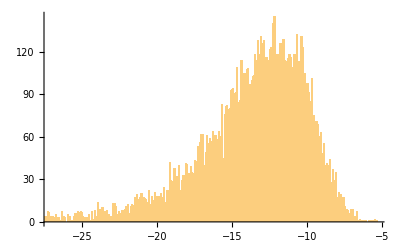

```mathematica
Histogram[Select[FitnessList,#>=-100&],1000]
```

#### State Analysis

```mathematica
<<StringyFNQuarksEnv`
SetOptions[StringyFNQuarksEnv,
{"nSinglet"->4,"nNonperts"->0,"nU1s"->5,"nChargeVec"->{1,1,1,1,1},"factorFitnessH"->1,"factorFitnessQ"->2,"factorFitnessCKM"->2,"factorFitnessGS"->30,"factorFitnessNAF"->30,"factorFitnessRG"->0.1,"factorFitnessTEX"->5,"factorFitnessO1"->0.02,"FitRange"->-20,"MethodGenOps"->"Graph","fitTextFac"->{1,0.25,1,4},"numOfO1Coeff"->20}];
fixO1coeffvec=Get["Documents/GitHub/string_inspired_MSSM_code/c_version/simlenv/current_ver_2.4.0/opts/o1coeff.txt"];
SetO1Coeff[fixO1coeffvec];
```

StringyFNQuarksEnv: RL/GA Environment for Froggatt-Nielsen Mass Model Building with Non-pertubative Effects

Last updated 16 Aug, 2024 by Lucas Leung.

Execute ?StringyFNQuarksEnv for help. Current StringyFNQuarksEnv options:

{nU1s→4,nChargeVec→{1,1,1,2},nSinglet→2,nNonperts→2,ΦChargeRange→{-7,8},DimOp→5,DimOpofΦ→2,bitsforϕ→3,bitsforΦ→3,BundleModuliFields→Global`ϕ,KahlerEffFields→Global`Φ,VEVsScale→Global`ϵ,ϕVEVmin→0.01,ϕVEVlogGen→1.01,ΦVEVmin→0.001,ΦVEVlogGen→1.01,fixedCharges→True,tenQ→{1,2,5},fiveBarHiggsQ→{4,5},O1CoeffRange→{0.5,3},numOfO1Coeff→10000,O1CoeffVarDiff→0.001,MethodGenOps→List,FitRange→-50,factorFitnessH→10,factorFitnessRG→1,factorFitnessQ→2,factorFitnessCKM→2,factorFitnessGS→20,factorFitnessNAF→20,factorFitnessTEX→10,factorFitnessO1→5,MaxLogPower→10,indPenal→False,diffPenal→False,indFitMax→1,fitDownFac→{1,1,1},fitUpFac→{1,1,1},fitCKMFac→{1,1,1,1,1,1,1,1,1},fitTextFac→{1,1,1,1},v→174,vErr→0.17,mu→{0.00216,1.27,172.69},md→{0.00467,0.0934,4.18},CKMmat→{{0.97373,0.2243,0.00382},{0.221,0.975,0.0408},{0.0086,0.0415,1.014}}}

```mathematica
listOfStates=Get["Desktop/model/data_analysis/n5-4p-fullruns-set1-old-states.m"];
listOfSV=Map[GAConvertBitlstStateVecFix[#[["Bitlist"]]]&,listOfStates];
```

```mathematica
listOfFS=Map[GAFitnessFuncQsector[#[["Bitlist"]]]&,listOfStates]
```

{<|Fitness→-22.6497,FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0,FitnessRGSec→6.01193,FitnessQMassSec→3.18653,FitnessQMixSec→1.1302,FitnessQmass→{1.14735,0.479021,0.,0.0290366,1.53112,0.},FitnessCKM→{0.0192666,0.209945,0.286891,0.21622,0.020498,0.11355,0.158803,0.0983692,0.0066605},FitnessGSSec→0,FitnessNAFSec→0,Hd→28.0927,Hu→146.551,Higgs→149.219,tanβ→5.21669,CKMmat→{{0.931477,0.363726,-0.00739528},{-0.36359,0.930051,-0.0529919},{0.0123966,-0.0520496,-0.998568}},md→{0.000332632,0.0309974,4.18},mu→{0.00202031,0.037384,172.69},FitnessO1List→{0.0262005,0.738936,1.47847,1.68493,0.,48.1886,2.1014,0.,0.229301,1.50311,1.33366,1.50092,0.231531,0.63908,3.08899,0.500637,0.00183664},FitnessO1Sec→63.2476,ValueLst→{0,3.18653,1.1302},ϕVEVs→{0.010303,0.0107214,0.0101,0.010201},ΦVEVs→{},YukdMatSt→(1.57224 ϕ[1] ϕ[3] ϕ[4] | 2.45663 ϕ[1] ϕ[3] ϕ[4] | -1.3332 ϕ[1] ϕ[3] ϕ[4]
1.39238 ϕ[2] ϕ[4] | -1.9314 ϕ[2] ϕ[4] | -1.89724 ϕ[2] ϕ[4]
-1.37332 ϕ[3] ϕ[4] | -2.86913 ϕ[3] ϕ[4] | 1. ϕ[3] ϕ[4]),YukuMatSt→(0.654717 ϕ[1]^2 ϕ[3] | -2.1288 ϕ[1] ϕ[2] | 0.840511 ϕ[1] ϕ[3]
-0.622308 ϕ[1] ϕ[2] | 0 | 1.34836 ϕ[2]
1.25873 ϕ[1] ϕ[3] | 2.71661 ϕ[2] | 3.32247 ϕ[3]),Bits→{1,0,1,1,1,1,0,1,0,1,1,1,1,1,0,1,0,0,0,1,0,1,0,1,0,1,0,0,1,0,1,0,0,0,1,0,1,1,0,0,0,0,0,0,1},StateVec→{1,2,5,1,2,1,2,1,2,4,5,5,4,4,3,1,2,5,4,3,7,1,2},Terminal→False,FitnessTextSec→2.43002,FitnessPowers→0,VarsScale→1.17379,ScalePenalty→1.95921,OTopPenalty→0.0443397,Qq→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},Qd→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qu→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QL→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qe→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QHd→{{0,0,0,1,1}},QHu→{{0,0,0,-1,-1}},Qϕ→{{-1,0,0,0,1},{0,-1,0,1,0},{0,0,0,1,-1},{0,0,1,-1,0}},QΦ→{},YukUpEigens→{1,7,13},YukDownEigens→{3,6,9},mtPow→1,mbPow→3,mu/mcPow→6,mc/mtPow→6,md/msPow→3,ms/mbPow→3,YukUpMatLead→{{ϵ^7,ϵ^10,ϵ^4},{ϵ^10,ϵ^40,ϵ^7},{ϵ^4,ϵ^7,ϵ}},YukDownMatLead→{{ϵ^6,ϵ^6,ϵ^6},{ϵ^9,ϵ^9,ϵ^9},{ϵ^3,ϵ^3,ϵ^3}},PosOTop→3,PosOBot→3,ListOfScales→{0.345495,0.440984,0.368403,0.281659},BestScale→0.354591,HiggsSquared→{237180.,8789.93},BestO1Top→3.32247,O1t^2→11.0388|>,<|Fitness→-17.6141,FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0,FitnessRGSec→11.3844,FitnessQMassSec→3.47553,FitnessQMixSec→3.36654,FitnessQmass→{1.87933,0.254083,0.,0.763286,0.578828,0.},FitnessCKM→{0.0112345,0.762569,0.324958,0.756461,0.0106262,0.460935,0.562863,0.47081,0.00608194},FitnessGSSec→0,FitnessNAFSec→0,Hd→43.8473,Hu→94.2325,Higgs→103.934,tanβ→2.1491,CKMmat→{{0.999247,0.038749,0.00180761},{-0.0387197,0.99915,-0.0141164},{0.00235307,-0.0140358,-0.999899}},md→{0.0000616579,0.16766,4.18},mu→{0.000372535,0.334946,172.69},FitnessO1List→{0.131835,0.740465,0.593112,0.538394,3.50363×10^-13,46.8474,0.814312,5.21991×10^-13,0.00131571,0.875714,0.696481,0.876463,0.00131683,1.57527,0.732844,1.58643,0.000312221},FitnessO1Sec→56.0117,ValueLst→{0,3.47553,3.36654},ϕVEVs→{0.0107214,0.0107214,0.0107214,0.0101},ΦVEVs→{},YukdMatSt→(1.57224 ϕ[1] ϕ[2] ϕ[3] ϕ[4] | 2.45663 ϕ[1] ϕ[2] ϕ[3] ϕ[4] | -1.3332 ϕ[1] ϕ[2] ϕ[3] ϕ[4]
1.39238 ϕ[1] ϕ[3] ϕ[4] | -1.9314 ϕ[1] ϕ[3] ϕ[4] | -1.89724 ϕ[1] ϕ[3] ϕ[4]
-1.37332 ϕ[1] ϕ[4] | -2.86913 ϕ[1] ϕ[4] | 1. ϕ[1] ϕ[4]),YukuMatSt→(0.654717 ϕ[2]^2 ϕ[3]^2 ϕ[4] | -2.1288 ϕ[2] ϕ[3]^2 ϕ[4] | 0.840511 ϕ[2] ϕ[3] ϕ[4]
-0.622308 ϕ[2] ϕ[3]^2 ϕ[4] | -1.50496 ϕ[3]^2 ϕ[4] | 1.34836 ϕ[3] ϕ[4]
1.25873 ϕ[2] ϕ[3] ϕ[4] | 2.71661 ϕ[3] ϕ[4] | 2.85466 ϕ[4]),Bits→{1,0,1,1,0,1,1,0,0,1,0,0,0,0,1,1,1,1,1,1,0,0,0,0,1,0,0,1,1,0,0,1,0,1,1,0,1,1,0,1,1,0,0,0,0},StateVec→{1,2,5,1,1,1,2,2,2,4,5,3,2,5,4,4,1,2,5,7,7,7,1},Terminal→True,FitnessTextSec→0.334258,FitnessPowers→0,VarsScale→1.07109,ScalePenalty→0.0664871,OTopPenalty→0,Qq→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},Qd→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qu→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QL→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qe→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QHd→{{0,0,0,1,1}},QHu→{{0,0,0,-1,-1}},Qϕ→{{0,0,1,-1,0},{-1,1,0,0,0},{0,-1,0,0,1},{0,0,0,1,-1}},QΦ→{},YukUpEigens→{1,15,29},YukDownEigens→{8,15,22},mtPow→1,mbPow→8,mu/mcPow→14,mc/mtPow→14,md/msPow→7,ms/mbPow→7,YukUpMatLead→{{ϵ^29,ϵ^22,ϵ^15},{ϵ^22,ϵ^15,ϵ^8},{ϵ^15,ϵ^8,ϵ}},YukDownMatLead→{{ϵ^22,ϵ^22,ϵ^22},{ϵ^15,ϵ^15,ϵ^15},{ϵ^8,ϵ^8,ϵ^8}},PosOTop→3,PosOBot→3,ListOfScales→{0.634146,0.70406,0.651836,0.580988},BestScale→0.641248,HiggsSquared→{72524.,21376.3},BestO1Top→2.85466,O1t^2→8.14907|>,<|Fitness→-18.3915,FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0,FitnessRGSec→6.01193,FitnessQMassSec→3.36515,FitnessQMixSec→1.3524,FitnessQmass→{1.14735,0.479021,0.,0.187757,1.55102,0.},FitnessCKM→{0.00932491,0.346603,0.268352,0.342379,0.00817485,0.113841,0.158747,0.0983157,0.00666035},FitnessGSSec→0,FitnessNAFSec→0,Hd→28.0927,Hu→146.551,Higgs→149.219,tanβ→5.21669,CKMmat→{{0.994863,0.100978,0.00708623},{-0.100465,0.993527,-0.0530275},{0.012395,-0.0520432,-0.998568}},md→{0.000332632,0.0309974,4.18},mu→{0.00140184,0.0357094,172.69},FitnessO1List→{0.0262005,0.738936,0.923626,0.88146,4.47106×10^-13,48.1886,2.1014,0.,0.0597184,5.78781,0.646898,5.80314,0.0612223,0.64025,3.08908,0.500717,0.00183641},FitnessO1Sec→69.4509,ValueLst→{0,3.36515,1.3524},ϕVEVs→{0.0106152,0.010201,0.010406,0.0101},ΦVEVs→{},YukdMatSt→(1.57224 ϕ[2] ϕ[3] | 2.45663 ϕ[2] ϕ[3] | -1.3332 ϕ[2] ϕ[3]
1.39238 ϕ[1] ϕ[2] ϕ[4] | -1.9314 ϕ[1] ϕ[2] ϕ[4] | -1.89724 ϕ[1] ϕ[2] ϕ[4]
-1.37332 ϕ[2] ϕ[4] | -2.86913 ϕ[2] ϕ[4] | 1. ϕ[2] ϕ[4]),YukuMatSt→(0 | -2.1288 ϕ[1] ϕ[3] | 0.840511 ϕ[3]
-0.622308 ϕ[1] ϕ[3] | -1.50496 ϕ[1]^2 ϕ[4] | 1.34836 ϕ[1] ϕ[4]
1.25873 ϕ[3] | 2.71661 ϕ[1] ϕ[4] | 3.32247 ϕ[4]),Bits→{0,0,1,0,1,0,1,1,1,0,1,0,1,1,0,1,1,0,0,0,1,1,1,1,1,0,1,0,0,1,0,1,1,1,0,1,0,0,1,0,1,1,0,0,0},StateVec→{1,2,5,2,2,1,1,1,2,4,5,5,3,4,4,2,4,1,5,6,2,4,1},Terminal→True,FitnessTextSec→1.39323,FitnessPowers→0,VarsScale→1.17379,ScalePenalty→0.922423,OTopPenalty→0.0443397,Qq→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},Qd→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qu→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QL→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qe→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QHd→{{0,0,0,1,1}},QHu→{{0,0,0,-1,-1}},Qϕ→{{0,-1,0,0,1},{0,0,1,-1,0},{-1,0,0,1,0},{0,0,0,1,-1}},QΦ→{},YukUpEigens→{1,7,13},YukDownEigens→{3,6,9},mtPow→1,mbPow→3,mu/mcPow→6,mc/mtPow→6,md/msPow→3,ms/mbPow→3,YukUpMatLead→{{ϵ^40,ϵ^10,ϵ^4},{ϵ^10,ϵ^13,ϵ^7},{ϵ^4,ϵ^7,ϵ}},YukDownMatLead→{{ϵ^6,ϵ^6,ϵ^6},{ϵ^9,ϵ^9,ϵ^9},{ϵ^3,ϵ^3,ϵ^3}},PosOTop→3,PosOBot→3,ListOfScales→{0.345495,0.440984,0.368403,0.281659},BestScale→0.354591,HiggsSquared→{237180.,8789.93},BestO1Top→3.32247,O1t^2→11.0388|>,<|Fitness→-17.6141,FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0,FitnessRGSec→11.3844,FitnessQMassSec→3.47553,FitnessQMixSec→3.36654,FitnessQmass→{1.87933,0.254083,0.,0.763286,0.578828,0.},FitnessCKM→{0.0112345,0.762569,0.324958,0.756461,0.0106262,0.460935,0.562863,0.47081,0.00608194},FitnessGSSec→0,FitnessNAFSec→0,Hd→43.8473,Hu→94.2325,Higgs→103.934,tanβ→2.1491,CKMmat→{{0.999247,0.038749,0.00180761},{-0.0387197,0.99915,-0.0141164},{0.00235307,-0.0140358,-0.999899}},md→{0.0000616579,0.16766,4.18},mu→{0.000372535,0.334946,172.69},FitnessO1List→{0.131835,0.740465,0.593112,0.538394,3.50363×10^-13,46.8474,0.814312,2.95857×10^-13,0.00131571,0.875714,0.696481,0.876463,0.00131683,1.57527,0.732844,1.58643,0.000312221},FitnessO1Sec→56.0117,ValueLst→{0,3.47553,3.36654},ϕVEVs→{0.0108286,0.0107214,0.0101,0.0107214},ΦVEVs→{},YukdMatSt→(1.57224 ϕ[1] ϕ[2] ϕ[4] | 2.45663 ϕ[1] ϕ[2] ϕ[4] | -1.3332 ϕ[1] ϕ[2] ϕ[4]
1.39238 ϕ[1] ϕ[2] | -1.9314 ϕ[1] ϕ[2] | -1.89724 ϕ[1] ϕ[2]
-1.37332 ϕ[1] | -2.86913 ϕ[1] | 1. ϕ[1]),YukuMatSt→(0.654717 ϕ[2]^2 ϕ[3] ϕ[4]^2 | -2.1288 ϕ[2]^2 ϕ[3] ϕ[4] | 0.840511 ϕ[2] ϕ[3] ϕ[4]
-0.622308 ϕ[2]^2 ϕ[3] ϕ[4] | -1.50496 ϕ[2]^2 ϕ[3] | 1.34836 ϕ[2] ϕ[3]
1.25873 ϕ[2] ϕ[3] ϕ[4] | 2.71661 ϕ[2] ϕ[3] | 2.85466 ϕ[3]),Bits→{0,0,1,0,0,1,0,1,1,1,1,0,0,1,1,0,0,1,1,0,0,1,1,1,1,1,0,0,0,0,1,1,0,1,1,1,1,1,0,0,0,0,1,1,0},StateVec→{1,2,5,2,1,2,1,2,1,4,5,3,5,4,2,5,2,5,1,8,7,1,7},Terminal→True,FitnessTextSec→0.334258,FitnessPowers→0,VarsScale→1.07109,ScalePenalty→0.0664871,OTopPenalty→0,Qq→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},Qd→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qu→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QL→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qe→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QHd→{{0,0,0,1,1}},QHu→{{0,0,0,-1,-1}},Qϕ→{{0,0,1,0,-1},{0,-1,0,0,1},{0,0,0,1,-1},{-1,1,0,0,0}},QΦ→{},YukUpEigens→{1,15,29},YukDownEigens→{8,15,22},mtPow→1,mbPow→8,mu/mcPow→14,mc/mtPow→14,md/msPow→7,ms/mbPow→7,YukUpMatLead→{{ϵ^29,ϵ^22,ϵ^15},{ϵ^22,ϵ^15,ϵ^8},{ϵ^15,ϵ^8,ϵ}},YukDownMatLead→{{ϵ^22,ϵ^22,ϵ^22},{ϵ^15,ϵ^15,ϵ^15},{ϵ^8,ϵ^8,ϵ^8}},PosOTop→3,PosOBot→3,ListOfScales→{0.634146,0.70406,0.651836,0.580988},BestScale→0.641248,HiggsSquared→{72524.,21376.3},BestO1Top→2.85466,O1t^2→8.14907|>,<|Fitness→-17.6951,FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0,FitnessRGSec→5.89936,FitnessQMassSec→3.45828,FitnessQMixSec→1.45014,FitnessQmass→{1.14735,0.479021,0.,0.303331,1.52858,0.},FitnessCKM→{0.0267776,0.253581,0.435038,0.259938,0.0281104,0.136599,0.178358,0.125,0.00674065},FitnessGSSec→0,FitnessNAFSec→0,Hd→28.0927,Hu→146.53,Higgs→149.199,tanβ→5.21595,CKMmat→{{0.915506,0.402171,-0.0104016},{-0.402096,0.913891,-0.0558803},{0.0129675,-0.0553412,-0.998383}},md→{0.000332632,0.0309974,4.18},mu→{0.00434295,0.0376033,172.69},FitnessO1List→{0.0262077,0.738936,1.60522,2.02884,3.50363×10^-13,48.1886,2.1014,4.10389×10^-13,0.257934,1.33585,1.27932,1.33352,0.260472,0.601719,3.10193,0.464687,0.00195148},FitnessO1Sec→63.3266,ValueLst→{0,3.45828,1.45014},ϕVEVs→{0.0101,0.010406,0.010303,0.0108286},ΦVEVs→{},YukdMatSt→(1.57224 ϕ[1] ϕ[2] ϕ[3] | 2.45663 ϕ[1] ϕ[2] ϕ[3] | -1.3332 ϕ[1] ϕ[2] ϕ[3]
1.39238 ϕ[1] ϕ[3] ϕ[4] | -1.9314 ϕ[1] ϕ[3] ϕ[4] | -1.89724 ϕ[1] ϕ[3] ϕ[4]
-1.37332 ϕ[1] ϕ[3] | -2.86913 ϕ[1] ϕ[3] | 1. ϕ[1] ϕ[3]),YukuMatSt→(0.654717 ϕ[1] ϕ[2]^2 | -2.1288 ϕ[1] ϕ[2] ϕ[4] | 0.840511 ϕ[1] ϕ[2]
-0.622308 ϕ[1] ϕ[2] ϕ[4] | -1.50496 ϕ[1] ϕ[4]^2 | 1.34836 ϕ[1] ϕ[4]
1.25873 ϕ[1] ϕ[2] | 2.71661 ϕ[1] ϕ[4] | 2.56385 ϕ[1]),Bits→{1,0,1,1,0,1,1,0,0,1,0,0,0,1,0,0,1,1,0,1,1,0,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,1,1,0,1,0,1,1,1},StateVec→{1,2,5,1,1,1,2,2,2,4,5,4,5,3,5,5,1,4,2,1,4,3,8},Terminal→True,FitnessTextSec→1.20435,FitnessPowers→0,VarsScale→1.1277,ScalePenalty→0.922423,OTopPenalty→0,Qq→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},Qd→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qu→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QL→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qe→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QHd→{{0,0,0,1,1}},QHu→{{0,0,0,-1,-1}},Qϕ→{{0,0,0,1,-1},{-1,0,0,0,1},{0,0,1,-1,0},{0,-1,0,0,1}},QΦ→{},YukUpEigens→{1,9,17},YukDownEigens→{4,8,12},mtPow→1,mbPow→4,mu/mcPow→8,mc/mtPow→8,md/msPow→4,ms/mbPow→4,YukUpMatLead→{{ϵ^9,ϵ^13,ϵ^5},{ϵ^13,ϵ^17,ϵ^9},{ϵ^5,ϵ^9,ϵ}},YukDownMatLead→{{ϵ^8,ϵ^8,ϵ^8},{ϵ^12,ϵ^12,ϵ^12},{ϵ^4,ϵ^4,ϵ^4}},PosOTop→3,PosOBot→3,ListOfScales→{0.450642,0.541149,0.472871,0.386627},BestScale→0.459511,HiggsSquared→{141235.,8789.93},BestO1Top→2.56385,O1t^2→6.57333|>,<|Fitness→-16.4094,FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0,FitnessRGSec→13.3508,FitnessQMassSec→4.05097,FitnessQMixSec→1.22481,FitnessQmass→{1.21547,0.687925,0.,0.185798,1.96177,0.},FitnessCKM→{0.0447319,0.328459,0.114986,0.334816,0.0455382,0.118885,0.0849094,0.146236,0.00625252},FitnessGSSec→0,FitnessNAFSec→0,Hd→47.0599,Hu→75.0828,Higgs→88.6118,tanβ→1.59547,CKMmat→{{0.878429,0.477847,-0.00497794},{-0.477758,0.877943,-0.0310295},{0.010457,-0.0296355,-0.999506}},md→{0.000284345,0.0191612,4.18},mu→{0.00140817,0.0138686,172.69},FitnessO1List→{0.208749,0.739867,1.00099,1.42316,4.47106×10^-13,48.1075,1.96665,0.,0.442519,1.49486,0.886222,1.49408,0.443405,0.650839,2.93742,0.367291,0.000644605},FitnessO1Sec→62.1642,ValueLst→{0,4.05097,1.22481},ϕVEVs→{0.0108286,0.0108286,0.0101,0.0106152},ΦVEVs→{},YukdMatSt→(1.57224 ϕ[1] ϕ[2] | 2.45663 ϕ[1] ϕ[2] | -1.3332 ϕ[1] ϕ[2]
1.39238 ϕ[1] ϕ[2] ϕ[4] | -1.9314 ϕ[1] ϕ[2] ϕ[4] | -1.89724 ϕ[1] ϕ[2] ϕ[4]
-1.37332 ϕ[1] | -2.86913 ϕ[1] | 1. ϕ[1]),YukuMatSt→(0.654717 ϕ[2]^2 ϕ[3] | -2.1288 ϕ[2]^2 ϕ[3] ϕ[4] | 0.840511 ϕ[2] ϕ[3]
-0.622308 ϕ[2]^2 ϕ[3] ϕ[4] | -1.50496 ϕ[2]^2 ϕ[3] ϕ[4]^2 | 1.34836 ϕ[2] ϕ[3] ϕ[4]
1.25873 ϕ[2] ϕ[3] | 2.71661 ϕ[2] ϕ[3] ϕ[4] | 3.61849 ϕ[3]),Bits→{1,0,1,1,1,1,0,1,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,1,0,1,0,1,1,1,1,1,1,0,0,0,1,0,1},StateVec→{1,2,5,1,2,1,2,1,2,4,5,3,5,4,1,5,1,5,2,8,8,1,6},Terminal→True,FitnessTextSec→0.655887,FitnessPowers→0,VarsScale→1.0906,ScalePenalty→0.057612,OTopPenalty→0.0814065,Qq→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},Qd→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qu→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QL→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qe→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QHd→{{0,0,0,1,1}},QHu→{{0,0,0,-1,-1}},Qϕ→{{0,0,1,0,-1},{-1,0,0,0,1},{0,0,0,1,-1},{1,-1,0,0,0}},QΦ→{},YukUpEigens→{1,17,29},YukDownEigens→{8,16,22},mtPow→1,mbPow→8,mu/mcPow→12,mc/mtPow→16,md/msPow→6,ms/mbPow→8,YukUpMatLead→{{ϵ^17,ϵ^23,ϵ^9},{ϵ^23,ϵ^29,ϵ^15},{ϵ^9,ϵ^15,ϵ}},YukDownMatLead→{{ϵ^16,ϵ^16,ϵ^16},{ϵ^22,ϵ^22,ϵ^22},{ϵ^8,ϵ^8,ϵ^8}},PosOTop→3,PosOBot→3,ListOfScales→{0.587788,0.735628,0.606962,0.621794},BestScale→0.635582,HiggsSquared→{73822.8,24637.9},BestO1Top→3.61849,O1t^2→13.0935|>,<|Fitness→-14.7576,FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0,FitnessRGSec→13.4853,FitnessQMassSec→3.30067,FitnessQMixSec→0.940196,FitnessQmass→{1.14735,0.479021,0.,0.12114,1.55316,0.},FitnessCKM→{0.0156973,0.184995,0.191452,0.191227,0.01688,0.100794,0.148447,0.0840833,0.00662138},FitnessGSSec→0,FitnessNAFSec→0,Hd→47.1769,Hu→74.0637,Higgs→87.8128,tanβ→1.56991,CKMmat→{{0.939164,0.343419,-0.0059363},{-0.343257,0.937831,-0.0514582},{0.0121044,-0.0503653,-0.998658}},md→{0.000332632,0.0309974,4.18},mu→{0.00163423,0.0355343,172.69},FitnessO1List→{0.213354,0.738936,1.11136,1.53426,3.50363×10^-13,48.1886,2.1014,0.,0.214739,1.60528,1.24803,1.60318,0.216824,0.660122,3.08188,0.520847,0.0017779},FitnessO1Sec→63.0406,ValueLst→{0,3.30067,0.940196},ϕVEVs→{0.0106152,0.0106152,0.0101,0.0106152},ΦVEVs→{},YukdMatSt→(1.57224 ϕ[1] ϕ[3] ϕ[4] | 2.45663 ϕ[1] ϕ[3] ϕ[4] | -1.3332 ϕ[1] ϕ[3] ϕ[4]
1.39238 ϕ[1] ϕ[2] ϕ[3] ϕ[4] | -1.9314 ϕ[1] ϕ[2] ϕ[3] ϕ[4] | -1.89724 ϕ[1] ϕ[2] ϕ[3] ϕ[4]
-1.37332 ϕ[1] ϕ[3] | -2.86913 ϕ[1] ϕ[3] | 1. ϕ[1] ϕ[3]),YukuMatSt→(0.654717 ϕ[3] ϕ[4]^2 | -2.1288 ϕ[2] ϕ[3] ϕ[4]^2 | 0.840511 ϕ[3] ϕ[4]
-0.622308 ϕ[2] ϕ[3] ϕ[4]^2 | -1.50496 ϕ[2]^2 ϕ[3] ϕ[4]^2 | 1.34836 ϕ[2] ϕ[3] ϕ[4]
1.25873 ϕ[3] ϕ[4] | 2.71661 ϕ[2] ϕ[3] ϕ[4] | 3.91501 ϕ[3]),Bits→{0,0,1,0,0,1,0,0,0,1,1,1,0,1,0,0,0,1,1,0,0,1,0,0,1,0,0,1,1,1,1,0,0,1,0,1,1,0,1,0,0,0,1,0,1},StateVec→{1,2,5,2,1,1,1,2,2,4,5,3,1,4,5,4,2,5,1,6,6,1,6},Terminal→True,FitnessTextSec→0.733301,FitnessPowers→0,VarsScale→1.08341,ScalePenalty→0,OTopPenalty→0.115612,Qq→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},Qd→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qu→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QL→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qe→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QHd→{{0,0,0,1,1}},QHu→{{0,0,0,-1,-1}},Qϕ→{{0,0,1,-1,0},{1,-1,0,0,0},{0,0,0,1,-1},{-1,0,0,0,1}},QΦ→{},YukUpEigens→{1,13,25},YukDownEigens→{7,13,19},mtPow→1,mbPow→7,mu/mcPow→12,mc/mtPow→12,md/msPow→6,ms/mbPow→6,YukUpMatLead→{{ϵ^13,ϵ^19,ϵ^7},{ϵ^19,ϵ^25,ϵ^13},{ϵ^7,ϵ^13,ϵ}},YukDownMatLead→{{ϵ^13,ϵ^13,ϵ^13},{ϵ^19,ϵ^19,ϵ^19},{ϵ^7,ϵ^7,ϵ^7}},PosOTop→3,PosOBot→3,ListOfScales→{0.587788,0.664066,0.606962,0.530715},BestScale→0.595476,HiggsSquared→{84102.,24788.9},BestO1Top→3.91501,O1t^2→15.3273|>}

```mathematica
listOfStates=Get["Desktop/model/data_analysis/n5-4p-fullruns-set1-save1-states.m"];
listOfSV=Map[GAConvertBitlstStateVecFix[#[["Bitlist"]]]&,listOfStates];
```

```mathematica
listOfFS=Map[GAFitnessFuncQsector[#[["Bitlist"]]]&,listOfStates]
```

{<|Fitness→-32.8725,FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0,FitnessRGSec→3.7073,FitnessQMassSec→3.44489,FitnessQMixSec→2.18867,FitnessQmass→{0.661101,1.42105,0.,1.04659,0.316151,0.},FitnessCKM→{0.00554814,0.0888641,0.0415518,0.0898355,0.0127891,0.627018,0.704936,0.605496,0.0126288},FitnessGSSec→0,FitnessNAFSec→0,Hd→16.8921,Hu→165.272,Higgs→166.133,tanβ→9.78401,CKMmat→{{0.96137,-0.275228,-0.00420354},{-0.271786,-0.946707,-0.172854},{0.0435947,0.167319,-0.984939}},md→{0.0214002,2.46261,4.18},mu→{0.024046,0.613272,172.69},FitnessO1List→{0.00816348,0.789304,0.534479,0.829476,0.,3.96582,0.974615,5.21991×10^-13,0.0714574,0.869621,10.7384,0.894289,0.0734835,1.63101,0.834856,1.6908,0.0504441},FitnessO1Sec→23.9562,ValueLst→{0,3.44489,2.18867},ϕVEVs→{0.0101,0.0105101,0.0106152,0.010303},ΦVEVs→{},YukdMatSt→(1.57224 ϕ[2] ϕ[3] | 2.45663 ϕ[2] ϕ[3] | 0
1.39238 ϕ[2] ϕ[4] | 1. ϕ[2] ϕ[4] | -1.89724 ϕ[2]
-1.37332 ϕ[2] | -2.86913 ϕ[2] | 0),YukuMatSt→(0.654717 ϕ[1] ϕ[2] ϕ[3]^2 | -2.1288 ϕ[1] ϕ[2] ϕ[3] ϕ[4] | 0.840511 ϕ[1] ϕ[2] ϕ[3]
-0.622308 ϕ[1] ϕ[2] ϕ[3] ϕ[4] | -1.50496 ϕ[1] ϕ[2] ϕ[4]^2 | 1.34836 ϕ[1] ϕ[2] ϕ[4]
1.25873 ϕ[1] ϕ[2] ϕ[3] | 2.71661 ϕ[1] ϕ[2] ϕ[4] | 22.6111 ϕ[1] ϕ[2]),Bits→{0,0,0,0,0,1,1,1,1,0,0,1,1,1,1,1,0,0,1,1,0,1,1,1,0,0,1,0,1,1,1,1,0,0,0,0,1,0,0,1,0,1,0,1,0},StateVec→{1,2,5,1,2,1,2,1,5,4,5,4,3,5,5,3,5,1,2,1,5,6,3},Terminal→False,FitnessTextSec→4.15111,FitnessPowers→0,VarsScale→2.56925,ScalePenalty→0,OTopPenalty→0.8772,Qq→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},Qd→{{1,1,0,0,0},{1,1,0,0,0},{1,0,0,0,1}},Qu→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QL→{{1,1,0,0,0},{1,1,0,0,0},{1,0,0,0,1}},Qe→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QHd→{{0,0,0,1,1}},QHu→{{0,0,0,-1,-1}},Qϕ→{{0,0,-1,1,0},{0,0,1,0,-1},{-1,0,0,0,1},{0,-1,0,0,1}},QΦ→{},YukUpEigens→{6,12,18},YukDownEigens→{5,8,8},mtPow→6,mbPow→5,mu/mcPow→6,mc/mtPow→6,md/msPow→0,ms/mbPow→3,YukUpMatLead→{{ϵ^18,ϵ^15,ϵ^12},{ϵ^15,ϵ^12,ϵ^9},{ϵ^12,ϵ^9,ϵ^6}},YukDownMatLead→{{ϵ^11,ϵ^11,ϵ^40},{ϵ^8,ϵ^8,ϵ^5},{ϵ^5,ϵ^5,ϵ^40}},PosOTop→3,PosOBot→2,ListOfScales→{0.345495,0.440984,3,0.281659},BestScale→0.599001,HiggsSquared→{1.39768×10^7,2938.19},BestO1Top→22.6111,O1t^2→511.261|>,<|Fitness→-20.2252,FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0,FitnessRGSec→1.47087,FitnessQMassSec→4.53013,FitnessQMixSec→0.802931,FitnessQmass→{0.625531,1.47137,0.,1.00673,1.42649,0.},FitnessCKM→{0.00773993,0.230215,0.0402962,0.224399,0.00698053,0.123703,0.0204772,0.142874,0.00624636},FitnessGSSec→0,FitnessNAFSec→0,Hd→22.8977,Hu→170.1,Higgs→171.634,tanβ→7.42869,CKMmat→{{0.991239,0.132012,0.0041914},{-0.131824,0.990798,-0.0306872},{0.00820392,-0.0298658,-0.99952}},md→{0.0197173,2.76517,4.18},mu→{0.0219375,0.0475676,172.69},FitnessO1List→{0.0136565,0.76699,0.545574,0.625339,3.50363×10^-13,1.54859,0.767273,3.35851×10^-13,0.0664367,3.73853,3.64714,3.74554,0.0665611,0.993653,0.79086,1.00529,0.000943259},FitnessO1Sec→18.3224,ValueLst→{0,4.53013,0.802931},ϕVEVs→{0.0105101,0.010303,0.0101,0.010201},ΦVEVs→{},YukdMatSt→(1. ϕ[2] | 2.45663 ϕ[1] ϕ[2] ϕ[3] | -1.3332 ϕ[1] ϕ[2] ϕ[3]
1.39238 ϕ[2] ϕ[4] | -1.9314 ϕ[1] ϕ[2] ϕ[3] ϕ[4] | -1.89724 ϕ[1] ϕ[2] ϕ[3] ϕ[4]
0 | -2.86913 ϕ[2] ϕ[3] | -1.5806 ϕ[2] ϕ[3]),YukuMatSt→(0.654717 ϕ[1]^2 ϕ[3] | -2.1288 ϕ[1]^2 ϕ[3] ϕ[4] | 0.840511 ϕ[1] ϕ[3]
-0.622308 ϕ[1]^2 ϕ[3] ϕ[4] | -1.50496 ϕ[1]^2 ϕ[3] ϕ[4]^2 | 1.34836 ϕ[1] ϕ[3] ϕ[4]
1.25873 ϕ[1] ϕ[3] | 2.71661 ϕ[1] ϕ[3] ϕ[4] | 2.08908 ϕ[3]),Bits→{1,1,1,0,0,0,1,1,1,1,1,0,0,1,0,0,1,0,1,1,1,1,0,1,1,0,1,0,1,1,1,0,0,1,0,0,0,1,0,0,0,0,0,0,1},StateVec→{1,2,5,2,2,2,4,1,1,4,5,5,3,4,1,1,4,5,2,5,3,1,2},Terminal→False,FitnessTextSec→1.80912,FitnessPowers→1,VarsScale→3.23646,ScalePenalty→0,OTopPenalty→0,Qq→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},Qd→{{0,1,0,1,0},{1,1,0,0,0},{1,1,0,0,0}},Qu→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QL→{{0,1,0,1,0},{1,1,0,0,0},{1,1,0,0,0}},Qe→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QHd→{{0,0,0,1,1}},QHu→{{0,0,0,-1,-1}},Qϕ→{{-1,0,0,0,1},{0,0,1,-1,0},{0,0,0,1,-1},{1,-1,0,0,0}},QΦ→{},YukUpEigens→{1,11,15},YukDownEigens→{3,5,4},mtPow→1,mbPow→3,mu/mcPow→4,mc/mtPow→10,md/msPow→-1,ms/mbPow→2,YukUpMatLead→{{ϵ^11,ϵ^13,ϵ^6},{ϵ^13,ϵ^15,ϵ^8},{ϵ^6,ϵ^8,ϵ}},YukDownMatLead→{{ϵ^3,ϵ^9,ϵ^9},{ϵ^5,ϵ^11,ϵ^11},{ϵ^40,ϵ^4,ϵ^4}},PosOTop→3,PosOBot→1,ListOfScales→{0.203078,0.611862,3,0.149481},BestScale→0.485854,HiggsSquared→{126335.,1328.37},BestO1Top→2.08908,O1t^2→4.36425|>,<|Fitness→-32.0585,FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0,FitnessRGSec→2.64655,FitnessQMassSec→2.30812,FitnessQMixSec→3.22971,FitnessQmass→{0.297927,1.41619,0.,0.549759,0.0442443,9.64327×10^-17},FitnessCKM→{0.0105987,0.528191,0.222217,0.539608,0.00393609,0.786867,0.340003,0.778262,0.0200261},FitnessGSSec→0,FitnessNAFSec→0,Hd→12.5926,Hu→168.979,Higgs→169.447,tanβ→13.4189,CKMmat→{{0.997786,0.066472,0.00229006},{-0.0637947,0.966203,-0.249763},{0.0188149,-0.249063,-0.968304}},md→{0.00927349,2.4352,4.18},mu→{0.00765972,1.4062,172.69},FitnessO1List→{0.00421777,0.763391,0.988026,0.879384,4.47106×10^-13,6.39916,0.940298,0.,0.0081497,1.85368,13.9277,1.99477,0.106609,1.59393,1.23392,1.59791,0.106047},FitnessO1Sec→32.3972,ValueLst→{0,2.30812,3.22971},ϕVEVs→{0.0106152,0.010303,0.010201,0.0106152},ΦVEVs→{},YukdMatSt→(1.57224 ϕ[1] ϕ[2] ϕ[4] | 2.45663 ϕ[1] ϕ[2] ϕ[4] | -1.3332 ϕ[1] ϕ[4]
1.39238 ϕ[2] ϕ[4] | 1. ϕ[2] ϕ[4] | -1.89724 ϕ[4]
-1.37332 ϕ[4] | -2.86913 ϕ[4] | 0),YukuMatSt→(0 | -2.1288 ϕ[1] ϕ[2]^2 ϕ[3] ϕ[4] | 0.840511 ϕ[1] ϕ[2] ϕ[3] ϕ[4]
-0.622308 ϕ[1] ϕ[2]^2 ϕ[3] ϕ[4] | -1.50496 ϕ[2]^2 ϕ[3] ϕ[4] | 1.34836 ϕ[2] ϕ[3] ϕ[4]
1.25873 ϕ[1] ϕ[2] ϕ[3] ϕ[4] | 2.71661 ϕ[2] ϕ[3] ϕ[4] | 21.2818 ϕ[3] ϕ[4]),Bits→{1,1,0,1,1,0,1,0,0,1,1,0,0,0,1,1,0,1,0,1,0,1,0,0,1,0,1,1,0,0,0,0,0,1,0,1,0,1,0,0,0,1,1,0,1},StateVec→{1,2,5,2,1,1,1,2,5,4,5,2,5,4,3,1,2,3,5,6,3,2,6},Terminal→False,FitnessTextSec→4.01406,FitnessPowers→0,VarsScale→2.44203,ScalePenalty→0,OTopPenalty→0.850887,Qq→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},Qd→{{1,1,0,0,0},{1,1,0,0,0},{1,0,0,0,1}},Qu→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QL→{{1,1,0,0,0},{1,1,0,0,0},{1,0,0,0,1}},Qe→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QHd→{{0,0,0,1,1}},QHu→{{0,0,0,-1,-1}},Qϕ→{{-1,1,0,0,0},{0,-1,0,0,1},{0,0,-1,1,0},{0,0,1,0,-1}},QΦ→{},YukUpEigens→{8,14,26},YukDownEigens→{6,9,9},mtPow→8,mbPow→6,mu/mcPow→12,mc/mtPow→6,md/msPow→0,ms/mbPow→3,YukUpMatLead→{{ϵ^40,ϵ^20,ϵ^17},{ϵ^20,ϵ^14,ϵ^11},{ϵ^17,ϵ^11,ϵ^8}},YukDownMatLead→{{ϵ^15,ϵ^15,ϵ^12},{ϵ^9,ϵ^9,ϵ^6},{ϵ^6,ϵ^6,ϵ^40}},PosOTop→3,PosOBot→2,ListOfScales→{0.587788,0.440984,3,0.281659},BestScale→0.684104,HiggsSquared→{1.29593×10^7,1662.98},BestO1Top→21.2818,O1t^2→452.916|>,<|Fitness→-16.957,FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0,FitnessRGSec→3.58087,FitnessQMassSec→2.93074,FitnessQMixSec→1.30973,FitnessQmass→{1.19812,0.320362,0.,0.185834,1.22643,0.},FitnessCKM→{0.0036762,0.0643374,0.431217,0.0706925,0.00579379,0.304599,0.125484,0.296391,0.00753604},FitnessGSSec→0,FitnessNAFSec→0,Hd→19.0671,Hu→161.806,Higgs→162.926,tanβ→8.48614,CKMmat→{{0.965522,0.260116,-0.0103105},{-0.260067,0.962079,-0.0822733},{0.0114811,-0.0821182,-0.996556}},md→{0.000295938,0.0446668,4.18},mu→{0.00331351,0.0754006,172.69},FitnessO1List→{0.0101012,0.737254,1.89104,2.3165,2.47689×10^-13,48.2377,2.18488,6.09642×10^-13,0.0975709,1.34305,1.92732,1.3383,0.102239,0.604722,3.18931,0.554318,0.00418777},FitnessO1Sec→64.5384,ValueLst→{0,2.93074,1.30973},ϕVEVs→{0.010303,0.010303,0.0101,0.0107214},ΦVEVs→{},YukdMatSt→(1.57224 ϕ[1] ϕ[2] | 2.45663 ϕ[1] ϕ[2] | -1.3332 ϕ[1] ϕ[2]
1.39238 ϕ[1] ϕ[4] | -1.9314 ϕ[1] ϕ[4] | -1.89724 ϕ[1] ϕ[4]
-1.37332 ϕ[1] | -2.86913 ϕ[1] | 1. ϕ[1]),YukuMatSt→(0.654717 ϕ[2]^2 ϕ[3] | -2.1288 ϕ[2] ϕ[3] ϕ[4] | 0.840511 ϕ[2] ϕ[3]
-0.622308 ϕ[2] ϕ[3] ϕ[4] | -1.50496 ϕ[3] ϕ[4]^2 | 1.34836 ϕ[3] ϕ[4]
1.25873 ϕ[2] ϕ[3] | 2.71661 ϕ[3] ϕ[4] | 2.64414 ϕ[3]),Bits→{1,1,1,0,0,0,1,1,0,0,0,0,0,1,0,0,0,1,0,0,1,0,1,0,1,1,0,0,1,0,1,1,0,0,1,0,0,1,0,0,0,0,1,1,0},StateVec→{1,2,5,2,2,2,1,1,1,4,5,3,5,4,5,5,1,5,2,3,3,1,7},Terminal→True,FitnessTextSec→1.36544,FitnessPowers→0,VarsScale→1.23228,ScalePenalty→1.05737,OTopPenalty→0,Qq→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},Qd→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qu→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QL→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qe→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QHd→{{0,0,0,1,1}},QHu→{{0,0,0,-1,-1}},Qϕ→{{0,0,1,0,-1},{-1,0,0,0,1},{0,0,0,1,-1},{0,-1,0,0,1}},QΦ→{},YukUpEigens→{1,7,15},YukDownEigens→{3,6,10},mtPow→1,mbPow→3,mu/mcPow→8,mc/mtPow→6,md/msPow→4,ms/mbPow→3,YukUpMatLead→{{ϵ^7,ϵ^11,ϵ^4},{ϵ^11,ϵ^15,ϵ^8},{ϵ^4,ϵ^8,ϵ}},YukDownMatLead→{{ϵ^6,ϵ^6,ϵ^6},{ϵ^10,ϵ^10,ϵ^10},{ϵ^3,ϵ^3,ϵ^3}},PosOTop→3,PosOBot→3,ListOfScales→{0.450642,0.440984,0.472871,0.281659},BestScale→0.403348,HiggsSquared→{183305.,4057.63},BestO1Top→2.64414,O1t^2→6.99147|>,<|Fitness→-14.4125,FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0,FitnessRGSec→2.79356,FitnessQMassSec→2.94634,FitnessQMixSec→2.89162,FitnessQmass→{1.87933,0.254083,0.,0.551909,0.261016,0.},FitnessCKM→{0.0113018,0.81267,0.358291,0.80696,0.0105786,0.179172,0.518698,0.187749,0.00619701},FitnessGSSec→0,FitnessNAFSec→0,Hd→16.743,Hu→164.317,Higgs→165.168,tanβ→9.81406,CKMmat→{{0.999402,0.034527,0.00167407},{-0.0344693,0.999041,-0.0270077},{0.00260496,-0.0269339,-0.999634}},md→{0.0000616579,0.16766,4.18},mu→{0.0006061,0.696286,172.69},FitnessO1List→{0.00761182,0.740465,0.598998,0.577042,2.21916×10^-13,46.8474,0.814312,3.34074×10^-13,0.000911067,0.764481,0.752184,0.766044,0.00103398,1.25441,0.76382,1.26048,0.000914778},FitnessO1Sec→55.1501,ValueLst→{0,2.94634,2.89162},ϕVEVs→{0.0106152,0.0101,0.0105101,0.0106152},ΦVEVs→{},YukdMatSt→(1.57224 ϕ[1] ϕ[3] ϕ[4] | 2.45663 ϕ[1] ϕ[3] ϕ[4] | -1.3332 ϕ[1] ϕ[3] ϕ[4]
1.39238 ϕ[1] ϕ[3] | -1.9314 ϕ[1] ϕ[3] | -1.89724 ϕ[1] ϕ[3]
-1.37332 ϕ[3] | -2.86913 ϕ[3] | 1. ϕ[3]),YukuMatSt→(0.654717 ϕ[1]^2 ϕ[2] ϕ[4]^2 | -2.1288 ϕ[1]^2 ϕ[2] ϕ[4] | 0.840511 ϕ[1] ϕ[2] ϕ[4]
-0.622308 ϕ[1]^2 ϕ[2] ϕ[4] | -1.50496 ϕ[1]^2 ϕ[2] | 1.34836 ϕ[1] ϕ[2]
1.25873 ϕ[1] ϕ[2] ϕ[4] | 2.71661 ϕ[1] ϕ[2] | 1.75973 ϕ[2]),Bits→{1,0,1,1,0,1,1,1,1,0,1,1,0,1,1,0,1,1,0,1,1,1,0,0,0,1,1,0,0,0,0,1,1,1,0,1,0,0,0,1,0,0,1,0,1},StateVec→{1,2,5,1,1,2,2,2,1,4,5,5,4,3,2,2,5,5,1,6,1,5,6},Terminal→True,FitnessTextSec→0.270854,FitnessPowers→0,VarsScale→1.08341,ScalePenalty→0,OTopPenalty→0,Qq→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},Qd→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qu→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QL→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qe→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QHd→{{0,0,0,1,1}},QHu→{{0,0,0,-1,-1}},Qϕ→{{0,-1,0,0,1},{0,0,0,1,-1},{0,0,1,0,-1},{-1,1,0,0,0}},QΦ→{},YukUpEigens→{1,13,25},YukDownEigens→{5,11,17},mtPow→1,mbPow→5,mu/mcPow→12,mc/mtPow→12,md/msPow→6,ms/mbPow→6,YukUpMatLead→{{ϵ^25,ϵ^19,ϵ^13},{ϵ^19,ϵ^13,ϵ^7},{ϵ^13,ϵ^7,ϵ}},YukDownMatLead→{{ϵ^17,ϵ^17,ϵ^17},{ϵ^11,ϵ^11,ϵ^11},{ϵ^5,ϵ^5,ϵ^5}},PosOTop→3,PosOBot→3,ListOfScales→{0.587788,0.664066,0.606962,0.530715},BestScale→0.595476,HiggsSquared→{84102.,3116.83},BestO1Top→1.75973,O1t^2→3.09664|>,<|Fitness→-24.6734,FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0,FitnessRGSec→3.67422,FitnessQMassSec→4.35374,FitnessQMixSec→2.43595,FitnessQmass→{1.25281,1.22468,0.,1.82766,0.0486052,0.},FitnessCKM→{0.000119328,0.00404128,0.350006,0.00432396,0.010158,0.70606,0.654329,0.691315,0.0155979},FitnessGSSec→0,FitnessNAFSec→0,Hd→17.9665,Hu→163.067,Higgs→164.054,tanβ→9.07616,CKMmat→{{0.973998,0.226397,-0.00855203},{-0.223211,0.95246,-0.207358},{0.0387997,-0.203875,-0.978228}},md→{0.0835841,1.56683,4.18},mu→{0.145248,1.42039,172.69},FitnessO1List→{0.00912519,0.760526,0.606009,1.02924,2.47689×10^-13,1.44687,0.849575,4.0313×10^-13,0.0233728,0.42924,3.99627,0.445161,0.0469017,1.15079,0.580946,1.18274,0.0520261},FitnessO1Sec→12.6088,ValueLst→{0,4.35374,2.43595},ϕVEVs→{0.0105101,0.010201,0.0106152,0.010303},ΦVEVs→{},YukdMatSt→(1. ϕ[1] ϕ[2] | 2.45663 ϕ[1] ϕ[2] ϕ[4] | -1.3332 ϕ[1] ϕ[2] ϕ[4]
1.39238 ϕ[1] ϕ[2] ϕ[3] | -1.9314 ϕ[1] ϕ[2] ϕ[3] ϕ[4] | -1.89724 ϕ[1] ϕ[2] ϕ[3] ϕ[4]
0 | -2.86913 ϕ[1] ϕ[2] | -1.5806 ϕ[1] ϕ[2]),YukuMatSt→(0.654717 ϕ[1] ϕ[4]^2 | -2.1288 ϕ[1] ϕ[3] ϕ[4]^2 | 0.840511 ϕ[1] ϕ[4]
-0.622308 ϕ[1] ϕ[3] ϕ[4]^2 | -1.50496 ϕ[1] ϕ[3]^2 ϕ[4]^2 | 1.34836 ϕ[1] ϕ[3] ϕ[4]
1.25873 ϕ[1] ϕ[4] | 2.71661 ϕ[1] ϕ[3] ϕ[4] | 7.05046 ϕ[1]),Bits→{0,0,1,0,0,1,1,1,0,0,0,1,0,0,0,0,1,0,1,1,1,0,1,0,1,0,1,0,1,1,1,0,0,1,0,0,0,0,1,1,0,1,0,1,0},StateVec→{1,2,5,2,1,2,5,2,1,4,5,4,3,1,5,5,4,2,1,5,2,6,3},Terminal→False,FitnessTextSec→2.09489,FitnessPowers→0,VarsScale→2.44203,ScalePenalty→0,OTopPenalty→0.371096,Qq→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},Qd→{{0,1,0,0,1},{1,1,0,0,0},{1,1,0,0,0}},Qu→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QL→{{0,1,0,0,1},{1,1,0,0,0},{1,1,0,0,0}},Qe→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QHd→{{0,0,0,1,1}},QHu→{{0,0,0,-1,-1}},Qϕ→{{0,0,0,1,-1},{0,0,1,-1,0},{1,-1,0,0,0},{-1,0,0,0,1}},QΦ→{},YukUpEigens→{5,11,23},YukDownEigens→{7,10,10},mtPow→5,mbPow→7,mu/mcPow→12,mc/mtPow→6,md/msPow→0,ms/mbPow→3,YukUpMatLead→{{ϵ^11,ϵ^17,ϵ^8},{ϵ^17,ϵ^23,ϵ^14},{ϵ^8,ϵ^14,ϵ^5}},YukDownMatLead→{{ϵ^7,ϵ^10,ϵ^10},{ϵ^13,ϵ^16,ϵ^16},{ϵ^40,ϵ^7,ϵ^7}},PosOTop→3,PosOBot→1,ListOfScales→{0.587788,0.440984,3,0.281659},BestScale→0.684104,HiggsSquared→{1.32835×10^6,3553.39},BestO1Top→7.05046,O1t^2→49.709|>,<|Fitness→-21.9119,FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0,FitnessRGSec→3.88611,FitnessQMassSec→3.03588,FitnessQMixSec→2.0673,FitnessQmass→{0.42528,1.42338,0.,1.12051,0.0667073,0.},FitnessCKM→{0.00342461,0.0680588,0.27207,0.0661191,0.00237196,0.576551,0.505324,0.562139,0.0112433},FitnessGSSec→0,FitnessNAFSec→0,Hd→19.8156,Hu→161.597,Higgs→162.807,tanβ→8.15502,CKMmat→{{0.981439,-0.191765,-0.00204171},{-0.18979,-0.969689,-0.15389},{0.027531,0.151421,-0.988086}},md→{0.0124336,2.47588,4.18},mu→{0.0285076,1.48085,172.69},FitnessO1List→{0.0118516,0.799699,0.554693,0.698548,4.47106×10^-13,3.96636,0.985095,3.34074×10^-13,0.031233,0.816868,12.2226,0.83545,0.036283,1.43584,0.763062,1.45984,0.0348853},FitnessO1Sec→24.6523,ValueLst→{0,3.03588,2.0673},ϕVEVs→{0.010201,0.010303,0.010406,0.010201},ΦVEVs→{},YukdMatSt→(1.57224 ϕ[2] ϕ[3] | 2.45663 ϕ[2] ϕ[3] | 0
1.39238 ϕ[2] ϕ[4] | 1. ϕ[2] ϕ[4] | -1.89724 ϕ[2]
-1.37332 ϕ[2] | -2.86913 ϕ[2] | 0),YukuMatSt→(0.654717 ϕ[1] ϕ[3]^2 | -2.1288 ϕ[1] ϕ[3] ϕ[4] | 0.840511 ϕ[1] ϕ[3]
-0.622308 ϕ[1] ϕ[3] ϕ[4] | -1.50496 ϕ[1] ϕ[4]^2 | 1.34836 ϕ[1] ϕ[4]
1.25873 ϕ[1] ϕ[3] | 2.71661 ϕ[1] ϕ[4] | 6.52505 ϕ[1]),Bits→{1,1,0,1,1,0,1,0,0,1,1,0,0,1,0,0,0,1,0,1,0,0,1,0,0,1,1,1,1,0,0,0,1,0,0,1,0,1,0,0,1,1,0,0,1},StateVec→{1,2,5,2,1,1,1,2,5,4,5,4,3,5,5,5,5,1,2,2,3,4,2},Terminal→False,FitnessTextSec→2.16477,FitnessPowers→0,VarsScale→3.25969,ScalePenalty→0,OTopPenalty→0.337463,Qq→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},Qd→{{1,1,0,0,0},{1,1,0,0,0},{1,0,0,0,1}},Qu→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QL→{{1,1,0,0,0},{1,1,0,0,0},{1,0,0,0,1}},Qe→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QHd→{{0,0,0,1,1}},QHu→{{0,0,0,-1,-1}},Qϕ→{{0,0,0,1,-1},{0,0,1,0,-1},{-1,0,0,0,1},{0,-1,0,0,1}},QΦ→{},YukUpEigens→{2,6,10},YukDownEigens→{3,5,5},mtPow→2,mbPow→3,mu/mcPow→4,mc/mtPow→4,md/msPow→0,ms/mbPow→2,YukUpMatLead→{{ϵ^10,ϵ^8,ϵ^6},{ϵ^8,ϵ^6,ϵ^4},{ϵ^6,ϵ^4,ϵ^2}},YukDownMatLead→{{ϵ^7,ϵ^7,ϵ^40},{ϵ^5,ϵ^5,ϵ^3},{ϵ^3,ϵ^3,ϵ^40}},PosOTop→3,PosOBot→2,ListOfScales→{0.203078,0.292843,3,0.149481},BestScale→0.404111,HiggsSquared→{1.11823×10^6,4011.88},BestO1Top→6.52505,O1t^2→42.5763|>,<|Fitness→-23.6051,FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0,FitnessRGSec→3.33685,FitnessQMassSec→4.62575,FitnessQMixSec→0.842733,FitnessQmass→{1.56113,1.37578,0.,1.49514,0.193702,9.64327×10^-17},FitnessCKM→{0.00115275,0.0166172,0.567415,0.0094118,0.000285432,0.044641,0.169782,0.0270526,0.00637574},FitnessGSSec→0,FitnessNAFSec→0,Hd→25.8364,Hu→164.809,Higgs→166.821,tanβ→6.37893,CKMmat→{{0.976318,0.21588,-0.0141084},{-0.216262,0.975641,-0.0368145},{0.00581723,0.0389938,0.999223}},md→{0.17,2.21884,4.18},mu→{0.0675452,1.98384,172.69},FitnessO1List→{0.0138046,0.575213,0.527336,0.714519,4.47106×10^-13,0.574897,0.602938,0.,0.0482275,0.984266,3.56998,0.983177,0.0481786,5.87303,3.98181,5.58335,0.00842099},FitnessO1Sec→24.0892,ValueLst→{0,4.62575,0.842733},ϕVEVs→{0.010303,0.0101,0.010406,0.0106152},ΦVEVs→{},YukdMatSt→(1.57224 ϕ[2] ϕ[3] ϕ[4] | 0 | -1.3332 ϕ[2] ϕ[3] ϕ[4]
1.39238 ϕ[1] ϕ[2] ϕ[3] | 1. ϕ[2] ϕ[3] | -1.89724 ϕ[1] ϕ[2] ϕ[3]
-1.37332 ϕ[2] ϕ[3] | 0 | -1.5806 ϕ[2] ϕ[3]),YukuMatSt→(0.654717 ϕ[3] ϕ[4]^2 | -2.1288 ϕ[1] ϕ[3] ϕ[4] | 0.840511 ϕ[3] ϕ[4]
-0.622308 ϕ[1] ϕ[3] ϕ[4] | -1.50496 ϕ[1]^2 ϕ[3] | 1.34836 ϕ[1] ϕ[3]
1.25873 ϕ[3] ϕ[4] | 2.71661 ϕ[1] ϕ[3] | 8.1129 ϕ[3]),Bits→{1,1,1,1,1,0,0,0,1,1,0,1,1,0,0,1,0,0,1,0,1,1,0,1,1,1,0,1,0,0,1,0,0,0,1,0,0,0,0,0,1,1,1,0,1},StateVec→{1,2,5,2,5,2,1,1,1,4,5,5,3,4,5,2,4,5,1,3,1,4,6},Terminal→False,FitnessTextSec→2.37053,FitnessPowers→0,VarsScale→2.56925,ScalePenalty→0,OTopPenalty→0.432055,Qq→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},Qd→{{1,1,0,0,0},{1,0,0,0,1},{1,1,0,0,0}},Qu→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QL→{{1,1,0,0,0},{1,0,0,0,1},{1,1,0,0,0}},Qe→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QHd→{{0,0,0,1,1}},QHu→{{0,0,0,-1,-1}},Qϕ→{{0,-1,0,0,1},{0,0,1,-1,0},{0,0,0,1,-1},{-1,0,0,0,1}},QΦ→{},YukUpEigens→{4,10,16},YukDownEigens→{5,8,8},mtPow→4,mbPow→5,mu/mcPow→6,mc/mtPow→6,md/msPow→0,ms/mbPow→3,YukUpMatLead→{{ϵ^16,ϵ^13,ϵ^10},{ϵ^13,ϵ^10,ϵ^7},{ϵ^10,ϵ^7,ϵ^4}},YukDownMatLead→{{ϵ^11,ϵ^40,ϵ^11},{ϵ^8,ϵ^5,ϵ^8},{ϵ^5,ϵ^40,ϵ^5}},PosOTop→3,PosOBot→2,ListOfScales→{0.345495,0.440984,3,0.281659},BestScale→0.599001,HiggsSquared→{1.79935×10^6,2938.19},BestO1Top→8.1129,O1t^2→65.8191|>,<|Fitness→-19.9335,FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0,FitnessRGSec→1.87542,FitnessQMassSec→3.79356,FitnessQMixSec→3.73539,FitnessQmass→{1.87933,0.254083,0.,0.895348,0.764796,0.},FitnessCKM→{0.0111894,0.734559,0.30577,0.72831,0.0106081,0.672098,0.583018,0.683783,0.00605509},FitnessGSSec→0,FitnessNAFSec→0,Hd→11.5617,Hu→169.571,Higgs→169.965,tanβ→14.6666,CKMmat→{{0.999144,0.0413305,0.00188927},{-0.0413126,0.999109,-0.00868086},{0.00224637,-0.00859537,-0.999961}},md→{0.0000616579,0.16766,4.18},mu→{0.000274856,0.218277,172.69},FitnessO1List→{0.00342765,0.740465,0.589455,0.611559,2.21916×10^-13,46.8474,0.814312,0.,0.00159458,0.93246,0.666297,0.932896,0.00159533,2.56148,0.717812,2.59069,0.000191095},FitnessO1Sec→58.0117,ValueLst→{0,3.79356,3.73539},ϕVEVs→{0.0107214,0.010303,0.010201,0.0107214},ΦVEVs→{},YukdMatSt→(1.57224 ϕ[1] ϕ[2] ϕ[3] ϕ[4] | 2.45663 ϕ[1] ϕ[2] ϕ[3] ϕ[4] | -1.3332 ϕ[1] ϕ[2] ϕ[3] ϕ[4]
1.39238 ϕ[2] ϕ[3] ϕ[4] | -1.9314 ϕ[2] ϕ[3] ϕ[4] | -1.89724 ϕ[2] ϕ[3] ϕ[4]
-1.37332 ϕ[2] ϕ[3] | -2.86913 ϕ[2] ϕ[3] | 1. ϕ[2] ϕ[3]),YukuMatSt→(0.654717 ϕ[1]^2 ϕ[2] ϕ[4]^2 | -2.1288 ϕ[1] ϕ[2] ϕ[4]^2 | 0.840511 ϕ[1] ϕ[2] ϕ[4]
-0.622308 ϕ[1] ϕ[2] ϕ[4]^2 | -1.50496 ϕ[2] ϕ[4]^2 | 1.34836 ϕ[2] ϕ[4]
1.25873 ϕ[1] ϕ[2] ϕ[4] | 2.71661 ϕ[2] ϕ[4] | 3.85984 ϕ[2]),Bits→{0,0,0,0,0,1,1,1,1,0,0,1,0,1,0,1,0,0,1,0,0,1,1,1,0,0,0,0,1,0,1,0,1,1,1,0,0,1,0,0,0,1,1,1,0},StateVec→{1,2,5,1,2,1,2,1,2,4,5,2,4,3,5,1,5,4,2,7,3,2,7},Terminal→True,FitnessTextSec→0.705565,FitnessPowers→0,VarsScale→1.07109,ScalePenalty→0,OTopPenalty→0.109448,Qq→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},Qd→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qu→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QL→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qe→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QHd→{{0,0,0,1,1}},QHu→{{0,0,0,-1,-1}},Qϕ→{{-1,1,0,0,0},{0,0,0,1,-1},{0,0,1,-1,0},{0,-1,0,0,1}},QΦ→{},YukUpEigens→{3,17,31},YukDownEigens→{5,12,19},mtPow→3,mbPow→5,mu/mcPow→14,mc/mtPow→14,md/msPow→7,ms/mbPow→7,YukUpMatLead→{{ϵ^31,ϵ^24,ϵ^17},{ϵ^24,ϵ^17,ϵ^10},{ϵ^17,ϵ^10,ϵ^3}},YukDownMatLead→{{ϵ^19,ϵ^19,ϵ^19},{ϵ^12,ϵ^12,ϵ^12},{ϵ^5,ϵ^5,ϵ^5}},PosOTop→3,PosOBot→3,ListOfScales→{0.634146,0.70406,0.651836,0.580988},BestScale→0.641248,HiggsSquared→{428921.,1486.25},BestO1Top→3.85984,O1t^2→14.8984|>,<|Fitness→-29.0419,FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0,FitnessRGSec→2.69633,FitnessQMassSec→4.68631,FitnessQMixSec→0.661888,FitnessQmass→{1.16566,0.373563,9.64327×10^-17,1.33281,1.81427,9.64327×10^-17},FitnessCKM→{0.00114146,0.0154818,0.265962,0.00952561,0.000149624,0.147607,0.0820065,0.13326,0.00675339},FitnessGSSec→0,FitnessNAFSec→0,Hd→12.2644,Hu→169.109,Higgs→169.554,tanβ→13.7887,CKMmat→{{0.976293,0.216445,-0.00207062},{-0.216205,0.974664,-0.0573149},{0.0103874,-0.0564038,-0.998354}},md→{0.000318899,0.039517,4.18},mu→{0.000100379,0.0194774,172.69},FitnessO1List→{0.00386259,0.737963,1.00297,1.08228,4.47106×10^-13,48.2234,2.16034,6.68149×10^-13,0.0978765,1.99051,1.13917,1.98784,0.100515,0.770448,3.10984,0.691477,0.00254421},FitnessO1Sec→63.1011,ValueLst→{0,4.68631,0.661888},ϕVEVs→{0.010406,0.0106152,0.0105101,0.0101},ΦVEVs→{},YukdMatSt→(1.57224 ϕ[1] ϕ[3] | 2.45663 ϕ[1] ϕ[3] | -1.3332 ϕ[1] ϕ[3]
1.39238 ϕ[1] ϕ[2] ϕ[3] | -1.9314 ϕ[1] ϕ[2] ϕ[3] | -1.89724 ϕ[1] ϕ[2] ϕ[3]
-1.37332 ϕ[1] | -2.86913 ϕ[1] | 1. ϕ[1]),YukuMatSt→(0.654717 ϕ[1] ϕ[3]^2 ϕ[4] | -2.1288 ϕ[1] ϕ[2] ϕ[3]^2 ϕ[4] | 0.840511 ϕ[1] ϕ[3] ϕ[4]
-0.622308 ϕ[1] ϕ[2] ϕ[3]^2 ϕ[4] | 0 | 1.34836 ϕ[1] ϕ[2] ϕ[3] ϕ[4]
1.25873 ϕ[1] ϕ[3] ϕ[4] | 2.71661 ϕ[1] ϕ[2] ϕ[3] ϕ[4] | 17.7013 ϕ[1] ϕ[4]),Bits→{1,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0,0,0,1,1,1,0,1,1,0,0,0,0,0},StateVec→{1,2,5,2,1,1,1,2,2,4,5,3,1,5,4,5,2,1,3,4,6,5,1},Terminal→False,FitnessTextSec→3.36276,FitnessPowers→0,VarsScale→1.11689,ScalePenalty→0,OTopPenalty→0.770885,Qq→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},Qd→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qu→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QL→{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},Qe→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QHd→{{0,0,0,1,1}},QHu→{{0,0,0,-1,-1}},Qϕ→{{0,0,1,0,-1},{1,-1,0,0,0},{-1,0,0,0,1},{0,0,-1,1,0}},QΦ→{},YukUpEigens→{5,15,27},YukDownEigens→{4,9,15},mtPow→5,mbPow→4,mu/mcPow→12,mc/mtPow→10,md/msPow→6,ms/mbPow→5,YukUpMatLead→{{ϵ^15,ϵ^21,ϵ^10},{ϵ^21,ϵ^40,ϵ^16},{ϵ^10,ϵ^16,ϵ^5}},YukDownMatLead→{{ϵ^9,ϵ^9,ϵ^9},{ϵ^15,ϵ^15,ϵ^15},{ϵ^4,ϵ^4,ϵ^4}},PosOTop→3,PosOBot→3,ListOfScales→{0.587788,0.611862,0.606962,0.467557},BestScale→0.56522,HiggsSquared→{8.96105×10^6,1677.3},BestO1Top→17.7013,O1t^2→313.338|>,<|Fitness→-24.5231,FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0,FitnessRGSec→1.97367,FitnessQMassSec→3.41377,FitnessQMixSec→2.06736,FitnessQmass→{1.27941,1.38987,0.,0.479768,0.264723,0.},FitnessCKM→{0.0110104,0.649178,0.311155,0.644014,0.0099466,0.0703852,0.303536,0.0615971,0.00653915},FitnessGSSec→0,FitnessNAFSec→0,Hd→16.5949,Hu→169.835,Higgs→170.644,tanβ→10.2342,CKMmat→{{0.998732,0.0503097,-0.00186599},{0.0501624,-0.997588,-0.0479784},{0.00427526,-0.0478239,0.998847}},md→{0.0888648,2.29202,4.18},mu→{0.00651961,2.33629,172.69},FitnessO1List→{0.00598566,0.576798,0.579161,0.771661,4.47106×10^-13,1.56253,0.609996,3.35851×10^-13,0.0055414,2.18493,4.67523,2.19151,0.0125087,5.27589,4.64959,5.2861,0.0121954},FitnessO1Sec→28.3996,ValueLst→{0,3.41377,2.06736},ϕVEVs→{0.010201,0.010406,0.010303,0.010303},ΦVEVs→{},YukdMatSt→(1.57224 ϕ[1] ϕ[2] ϕ[4] | 2.45663 ϕ[2] ϕ[4] | -1.3332 ϕ[1] ϕ[2] ϕ[4]
1.39238 ϕ[1] ϕ[4] | 1. ϕ[4] | -1.89724 ϕ[1] ϕ[4]
-1.37332 ϕ[4] | 0 | -1.5806 ϕ[4]),YukuMatSt→(0.654717 ϕ[1]^2 ϕ[2]^2 ϕ[3] | -2.1288 ϕ[1]^2 ϕ[2] ϕ[3] | 0.840511 ϕ[1] ϕ[2] ϕ[3]
-0.622308 ϕ[1]^2 ϕ[2] ϕ[3] | -1.50496 ϕ[1]^2 ϕ[3] | 1.34836 ϕ[1] ϕ[3]
1.25873 ϕ[1] ϕ[2] ϕ[3] | 2.71661 ϕ[1] ϕ[3] | 8.44254 ϕ[3]),Bits→{0,0,1,0,0,1,0,0,1,0,1,0,0,0,1,0,0,1,1,0,0,1,0,1,0,1,1,0,1,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0},StateVec→{1,2,5,2,1,1,1,5,2,4,5,5,2,4,3,2,1,5,5,2,4,3,3},Terminal→False,FitnessTextSec→2.55909,FitnessPowers→0,VarsScale→3.04672,ScalePenalty→0,OTopPenalty→0.449352,Qq→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},Qd→{{1,1,0,0,0},{1,0,0,0,1},{1,1,0,0,0}},Qu→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QL→{{1,1,0,0,0},{1,0,0,0,1},{1,1,0,0,0}},Qe→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QHd→{{0,0,0,1,1}},QHu→{{0,0,0,-1,-1}},Qϕ→{{0,-1,0,0,1},{-1,1,0,0,0},{0,0,0,1,-1},{0,0,1,0,-1}},QΦ→{},YukUpEigens→{3,7,15},YukDownEigens→{3,5,5},mtPow→3,mbPow→3,mu/mcPow→8,mc/mtPow→4,md/msPow→0,ms/mbPow→2,YukUpMatLead→{{ϵ^15,ϵ^11,ϵ^9},{ϵ^11,ϵ^7,ϵ^5},{ϵ^9,ϵ^5,ϵ^3}},YukDownMatLead→{{ϵ^9,ϵ^7,ϵ^9},{ϵ^5,ϵ^3,ϵ^5},{ϵ^3,ϵ^40,ϵ^3}},PosOTop→3,PosOBot→2,ListOfScales→{0.450642,0.292843,3,0.149481},BestScale→0.493223,HiggsSquared→{2.07146×10^6,1213.65},BestO1Top→8.44254,O1t^2→71.2764|>,<|Fitness→-24.6409,FitnessHSec→0,FitnessHiggs→0,FitnessTanβ→0,FitnessRGSec→4.67147,FitnessQMassSec→3.41866,FitnessQMixSec→1.83459,FitnessQmass→{0.935085,1.1919,0.,0.986387,0.30529,0.},FitnessCKM→{0.00681769,0.183653,0.00924518,0.180451,0.00133489,0.562883,0.326921,0.552354,0.0109244},FitnessGSSec→0,FitnessNAFSec→0,Hd→21.4089,Hu→158.885,Higgs→160.321,tanβ→7.42145,CKMmat→{{0.989137,0.146952,-0.00373954},{-0.145862,0.978001,-0.149123},{0.0182566,-0.148048,-0.988812}},md→{0.0402163,1.45294,4.18},mu→{0.0209335,0.628802,172.69},FitnessO1List→{0.0136277,0.763912,0.708281,1.13256,2.47689×10^-13,1.47961,0.826996,0.,0.0119826,0.541028,4.32217,0.551285,0.0258914,1.20681,0.540856,1.21989,0.0275161},FitnessO1Sec→13.3724,ValueLst→{0,3.41866,1.83459},ϕVEVs→{0.010406,0.010406,0.010303,0.010201},ΦVEVs→{},YukdMatSt→(1. ϕ[2] | 2.45663 ϕ[2] ϕ[4] | -1.3332 ϕ[2] ϕ[4]
1.39238 ϕ[1] ϕ[2] | -1.9314 ϕ[1] ϕ[2] ϕ[4] | -1.89724 ϕ[1] ϕ[2] ϕ[4]
0 | -2.86913 ϕ[2] | -1.5806 ϕ[2]),YukuMatSt→(0.654717 ϕ[3] ϕ[4]^2 | -2.1288 ϕ[1] ϕ[3] ϕ[4]^2 | 0.840511 ϕ[3] ϕ[4]
-0.622308 ϕ[1] ϕ[3] ϕ[4]^2 | -1.50496 ϕ[1]^2 ϕ[3] ϕ[4]^2 | 1.34836 ϕ[1] ϕ[3] ϕ[4]
1.25873 ϕ[3] ϕ[4] | 2.71661 ϕ[1] ϕ[3] ϕ[4] | 9.05084 ϕ[3]),Bits→{0,0,1,0,0,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,0,0,1,0,1,0,0,1,0,0,1,0,1,0,1,1,0,1,1,0,1,0,0,0,1},StateVec→{1,2,5,2,1,2,5,2,1,4,5,1,3,4,5,2,5,5,1,4,4,3,2},Terminal→False,FitnessTextSec→2.67995,FitnessPowers→0,VarsScale→3.04672,ScalePenalty→0,OTopPenalty→0.479568,Qq→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},Qd→{{0,1,0,0,1},{1,1,0,0,0},{1,1,0,0,0}},Qu→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QL→{{0,1,0,0,1},{1,1,0,0,0},{1,1,0,0,0}},Qe→{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1}},QHd→{{0,0,0,1,1}},QHu→{{0,0,0,-1,-1}},Qϕ→{{1,-1,0,0,0},{0,0,1,0,-1},{0,0,0,1,-1},{-1,0,0,0,1}},QΦ→{},YukUpEigens→{3,7,15},YukDownEigens→{4,6,6},mtPow→3,mbPow→4,mu/mcPow→8,mc/mtPow→4,md/msPow→0,ms/mbPow→2,YukUpMatLead→{{ϵ^7,ϵ^11,ϵ^5},{ϵ^11,ϵ^15,ϵ^9},{ϵ^5,ϵ^9,ϵ^3}},YukDownMatLead→{{ϵ^4,ϵ^6,ϵ^6},{ϵ^8,ϵ^10,ϵ^10},{ϵ^40,ϵ^4,ϵ^4}},PosOTop→3,PosOBot→1,ListOfScales→{0.450642,0.292843,3,0.149481},BestScale→0.493223,HiggsSquared→{2.07146×10^6,4988.94},BestO1Top→9.05084,O1t^2→81.9178|>}